## clearing variables

```mathematica
NotebookDelete[Cells[EvaluationNotebook[],GeneratedCell->True]]
```

## setup

```mathematica
cutoff = 40;
```

```mathematica
datapath = "Dropbox/mini_seventeen/ResearchMalaria/newdata2020/CXCR3CCR5KO/20_1111 KO CTV WT CMPTX/Mouse 2";
(*datapath = "Dropbox/mini_seventeen/ResearchMalaria/newdata2020/160920";*)
(*datapath = "Dropbox/mini_seventeen/ResearchMalaria/Cluster_formation-early-movies_July21/T_Cell_Dynamics_Parasite_Present/Video_2_with_analysis";*)
datasetname = "Mouse 2";
cellsfilename = "CXCR3 CCR5 KO cells.xls";
parasitefilename = "Parasite.xls";
(*timestep=0.25;*)
```

```mathematica
hassecond = True;
secondsetfilename="Wild type OT1 cells.xls";
```

```mathematica
(*boxsizex = 512;
boxsizey = 512;
boxsizez = 46;
boxvolume = boxsizex*boxsizey*boxsizez;*)
livervolume = 10000^3;
```

```mathematica
Remove[k]
Remove[z]
anglePDF=1/2 ⅇ^(k Cos[z]) k Abs[Sin[z]] Csch[k];
```

```mathematica
mixPDF=1/2 ⅇ^(k1 Cos[z]) k1 10^w1 Abs[Sin[z]] Csch[k1]+1/2 ⅇ^(k2 Cos[z]) k2 (1-10^w1) Abs[Sin[z]] Csch[k2];
```

```mathematica
getClosestCell[cellNo_,list_] :=  
{fpp = FirstPosition[list[[cellNo]], x_ /; x ≠ {0}] ;
fpValue = Extract[list[[cellNo]], fpp] ;
ourList = Select[First /@ Evaluate[(Part[#,fpp])&  /@ list], # ≠ {0}&];
listOfDistpp = Select[(EuclideanDistance[#,fpValue])& /@ ourList, # ≠ 0&];
closestDistance = Min[listOfDistpp];
closestDistance}
```

```mathematica
SetDirectory[]
PicturesPath="/Dropbox/mini_seventeen/ResearchMalaria/Ganusov/reextraquestions/";
Get["Dropbox/mini_seventeen/ResearchMalaria/Ganusov/reextraquestions/bootstrap-2r.m"]
Get["Dropbox/mini_seventeen/ResearchMalaria/Ganusov/reextraquestions/graphics-12.m"]
Get["Dropbox/mini_seventeen/ResearchMalaria/Ganusov/reextraquestions/tests.m"]
Get["Dropbox/mini_seventeen/ResearchMalaria/Ganusov/reextraquestions/tools.m"]
```

/Users/viktor

```mathematica
histPlot[data_,bins_,color_: Blue]:=Module[{countBorder=Partition[Riffle[Riffle[#1,#1[[2;;]]],Riffle[#2,#2]],2]&@@HistogramList[data,bins,"Probability"]},ListLinePlot[countBorder,PlotStyle->color,PlotRange->All]];
```

```mathematica
ticksXKShort[min_,max_]:=Table[{i,Style[i,14],{.04,0},Thick},{i,min,max}];
ticksYKShort[min_,max_]:=Table[{i,Style[i,14],{.04,0},Thick},{i,min,max, 0.1}];
```

```mathematica
(* fitting vMF distribution to data *)

Clear[P,L1];

P[phi_,{kappa_}]:=kappa*Sin[phi]*Exp[kappa*Cos[phi]]/(2*Sinh[kappa]);
P0[phi_,{n_}]:=((Sin[phi])^n)/((√π Gamma[(1+n)/2])/Gamma[1+n/2]);
pmin=10^-15;
FitOneVMF[dataset_,{kappa_}]:=-Total[Map[Log[pmin+P[#,{kappa}]]&,dataset]];
FitTwoVMF[dataset_,{kappa1_,kappa2_,f_}]:=-Total[Map[Log[pmin+f*P[#,{kappa1}]+(1-f)*P[#,{kappa2}]]&,dataset]]+10^(-10*(1-f));
FitVMFSin[dataset_,{kappa1_,n_,f_}]:=-Total[Map[Log[pmin+f*P[#,{kappa1}]+(1-f)*P0[#,{n}]]&,dataset]]+10^(-10*(1-f));
```

## importing positions

```mathematica
SetDirectory[];
SetDirectory[datapath];
```

```mathematica
genericfirst = Import[cellsfilename, {"Sheets", "Position"}];
genericfirstData = Rest[Rest[genericfirst]];
genericfirstAssociation = AssociationThread[ToString/@genericfirst[[2]] -> Range[Length[genericfirst[[2]]]]];

(*hardcoded: the associations' labels*)
originalParent= Min[genericfirstData[[All,genericfirstAssociation["TrackID"]]]];
genericfirstPoints = genericfirstData[[;;,{genericfirstAssociation[["Position X"]], genericfirstAssociation[["Position Y"]], genericfirstAssociation[["Position Z"]]}]];

(*hardcoded: the 10^9-1 offset of the number of cells*)
numcells = Max[genericfirstData[[;;,{genericfirstAssociation[["TrackID"]]}]] - originalParent] + 1;
numtimes = Max[genericfirstData[[;;,{genericfirstAssociation[["Time"]]}]]];
genericfirstPositions = Table[Table[{0},{i3,numtimes}],{i2,numcells}];
Do[genericfirstPositions[[genericfirstData[[i2]][[genericfirstAssociation[["TrackID"]]]] - originalParent+1]][[genericfirstData[[i2]][[genericfirstAssociation[["Time"]]]]]] = {genericfirstData[[i2]][[1]],genericfirstData[[i2]][[2]],genericfirstData[[i2]][[3]]},{i2,Length[genericfirstData]}];
```

```mathematica
If[hassecond,

genericsecond = Import[secondsetfilename, {"Sheets", "Position"}];
genericsecondData = Rest[Rest[genericsecond]];
genericsecondAssociation = AssociationThread[ToString/@genericsecond[[2]] -> Range[Length[genericsecond[[2]]]]];

originalParent= genericsecondData[[1]][[genericsecondAssociation["TrackID"]]];
genericsecondPoints = genericsecondData[[;;,{genericsecondAssociation[["Position X"]], genericsecondAssociation[["Position Y"]], genericsecondAssociation[["Position Z"]]}]];

numcells = Max[genericsecondData[[;;,{genericsecondAssociation[["TrackID"]]}]] - 10^9] + 1;
numtimes = Max[genericsecondData[[;;,{genericsecondAssociation[["Time"]]}]]];
genericsecondPositions = Table[Table[{0},{i3,numtimes}],{i2,numcells}];
Do[genericsecondPositions[[genericsecondData[[i2]][[genericsecondAssociation[["TrackID"]]]] - 10^9+1]][[genericsecondData[[i2]][[genericsecondAssociation[["Time"]]]]]] = {genericsecondData[[i2]][[1]],genericsecondData[[i2]][[2]],genericsecondData[[i2]][[3]]},{i2,Length[genericsecondData]}];,

Remove[genericsecond];
Remove[genericsecondData];
Remove[genericsecondAssociation];
Remove[genericsecondPoints];
Remove[genericsecondPositions];
];
```

```mathematica
genericParasite = Import[parasitefilename, {"Sheets", "Position"}];
genericParasiteData = Rest[Rest[genericParasite]];
genericParasiteAssociation = AssociationThread[ToString/@genericParasite[[2]] -> Range[Length[genericParasite[[2]]]]];
originalParent= genericParasiteData[[1]][[genericParasiteAssociation["TrackID"]]];
genericParasitePoints = genericParasiteData[[;;,{genericParasiteAssociation[["Position X"]], genericParasiteAssociation[["Position Y"]], genericParasiteAssociation[["Position Z"]]}]];

numcells = Max[genericParasiteData[[;;,{genericParasiteAssociation[["TrackID"]]}]] - 10^9] + 1;
numparasites = numcells;
numtimes = If[hassecond,Max[{genericfirstData[[;;,{genericfirstAssociation[["Time"]]}]],genericsecondData[[;;,{genericfirstAssociation[["Time"]]}]]}],Max[genericfirstData[[;;,{genericfirstAssociation[["Time"]]}]]]];
genericParasitePositions = Table[Table[{0},{i3,numtimes}],{i2,numcells}];

Do[genericParasitePositions[[genericParasiteData[[i2]][[genericParasiteAssociation[["TrackID"]]]] - 10^9+1]][[genericParasiteData[[i2]][[genericParasiteAssociation[["Time"]]]]]] = {genericParasiteData[[i2]][[1]],genericParasiteData[[i2]][[2]],genericParasiteData[[i2]][[3]]},{i2,Length[genericParasiteData]}];
Do[
bindex=0;
Do[If[genericParasitePositions[[ind]][[ii]][[1]]==0,genericParasitePositions[[ind]][[ii]]=genericParasitePositions[[ind]][[ii-1]]];
If[genericParasitePositions[[ind]][[ii]]==List,bindex=ii],{ii,Length[genericParasitePositions[[ind]]]}];
Do[genericParasitePositions[[ind]][[ii]]=genericParasitePositions[[ind]][[ii+1]],{ii,bindex,1,-1}]

,{ind,Length[genericParasitePositions]}];
```

## timestep

```mathematica
generictimes = Import[cellsfilename, {"Sheets", "Time"}];
generictimesteps = Sort[Union[generictimes[[All,1]][[3;;]]]];
timestep = Mean[Table[generictimesteps[[ii+1]]-generictimesteps[[ii]],{ii,Length[generictimesteps]-1}]];
```

## distances

```mathematica
numcells = Max[genericfirstData[[;;,{genericfirstAssociation[["TrackID"]]}]] - 10^9] + 1;
numtimes = Max[genericfirstData[[;;,{genericfirstAssociation[["Time"]]}]]];

genericfirstDistances = Table[Table[Table["N",numtimes],numcells],numparasites];

Do[Do[genericfirstDistances[[ind]][[genericfirstData[[i2]][[genericfirstAssociation["TrackID"] ]] - originalParent + 1]][[genericfirstData[[i2]][[genericfirstAssociation["Time"] ]] ]]  = EuclideanDistance[{genericfirstData[[i2]][[genericfirstAssociation["Position X"] ]],   genericfirstData[[i2]][[genericfirstAssociation["Position Y"] ]],   genericfirstData[[i2]][[genericfirstAssociation["Position Z"] ]]},       genericParasitePositions[[ind]][[genericfirstData[[i2]][[genericParasiteAssociation["Time"] ]] ]]], {i2,Length[genericfirstData]}],{ind,numparasites}];
```

```mathematica
If[hassecond,

numcells = Max[genericsecondData[[;;,{genericsecondAssociation[["TrackID"]]}]] - 10^9] + 1;
numtimes = Max[genericsecondData[[;;,{genericsecondAssociation[["Time"]]}]]];
genericsecondDistances = Table[Table[Table["N",numtimes],numcells],numparasites];
Do[Do[genericsecondDistances[[ind]][[genericsecondData[[i2]][[genericsecondAssociation["TrackID"] ]] - originalParent + 1]][[genericsecondData[[i2]][[genericsecondAssociation["Time"] ]] ]]  = EuclideanDistance[{genericsecondData[[i2]][[genericsecondAssociation["Position X"] ]],   genericsecondData[[i2]][[genericsecondAssociation["Position Y"] ]],   genericsecondData[[i2]][[genericsecondAssociation["Position Z"] ]]},       genericParasitePositions[[ind]][[genericsecondData[[i2]][[genericParasiteAssociation["Time"] ]] ]]], {i2,Length[genericsecondData]}],{ind,numparasites}];,

Remove[genericsecondDistances]
];
```

## changes of distance

```mathematica
genericParasiteMean = Table[Mean[genericParasitePositions[[ind]]],{ind,Range[numparasites]}];
genericParasiteError =Table[Map[(#-genericParasiteMean[[ind]])&,genericParasitePositions[[ind]]],{ind,numparasites}];
genericfirstDistancesWithoutN =Table[ DeleteCases[genericfirstDistances[[ind]], "N", {1,5}],{ind,numparasites}];
genericfirstStartingDistances = genericfirstDistancesWithoutN[[All,All,1]];
(* replace all the N's in Positions with {n,n,n}'s *)

genericfirstInBetween = genericfirstPositions/.{0}-> {n,n,n} ;
(* subtract the error from InBetween. PositionsCorrected now holds the positions corrected for parasite recording error, and the N's are replaced by {n+err,n+err,n+err}'s. *)
genericfirstPositionsCorrected = Table[Table[Table[genericfirstInBetween[[i1]][[i2]] - genericParasiteError[[ind]][[i2]],{i2,Length[genericfirstInBetween[[i1]] ]}],{i1,Length[genericfirstInBetween]}],{ind,numparasites}];
(* this goes through PositionsCorrected and removes the entries with n+err's. *)

genericfirstCorrectedWithout0= DeleteCases[genericfirstPositionsCorrected, {n+_,_,_}, {1,4}];
genericfirstChangesV2 = Table[Table[Table[(genericfirstDistancesWithoutN[[ind]][[i1]][[j1+1]] - genericfirstDistancesWithoutN[[ind]][[i1]][[j1]]),{j1,Length[genericfirstDistancesWithoutN[[ind]][[i1]]]-1}],{i1,Length[genericfirstDistancesWithoutN[[ind]]]}],{ind,numparasites}];
genericfirstChangeV2Positive = Table[Count[Flatten[genericfirstChangesV2[[ind]]], u_ /; u > 0],{ind,numparasites}];
genericfirstChangeV2Negative = Table[Count[Flatten[genericfirstChangesV2[[ind]]], u_ /; u < 0],{ind,numparasites}];
```

```mathematica
If[hassecond,

genericsecondDistancesWithoutN =Table[ DeleteCases[genericsecondDistances[[ind]], "N", {1,5}],{ind,numparasites}];
genericsecondStartingDistances = genericsecondDistancesWithoutN[[All,All,1]];
genericsecondInBetween = genericsecondPositions/.{0}-> {n,n,n};
Table[Table[Table[genericsecondInBetween[[i1]][[i2]] - genericParasiteError[[ind]][[i2]],{i2,Length[genericsecondInBetween[[i1]] ]}],{i1,Length[genericsecondInBetween]}],{ind,numparasites}];
genericsecondPositionsCorrected = Table[Table[Table[genericsecondInBetween[[i1]][[i2]] - genericParasiteError[[ind]][[i2]],{i2,Length[genericsecondInBetween[[i1]] ]}],{i1,Length[genericsecondInBetween]}],{ind,numparasites}];
genericsecondCorrectedWithout0= DeleteCases[genericsecondPositionsCorrected, {n+_,_,_}, {1,4}];
genericsecondChangesV2 = Table[Table[Table[(genericsecondDistancesWithoutN[[ind]][[i1]][[j1+1]] - genericsecondDistancesWithoutN[[ind]][[i1]][[j1]]),{j1,Length[genericsecondDistancesWithoutN[[ind]][[i1]]]-1}],{i1,Length[genericsecondDistancesWithoutN[[ind]]]}],{ind,numparasites}];
genericsecondChangeV2Positive = Table[Count[Flatten[genericsecondChangesV2[[ind]]], u_ /; u > 0],{ind,numparasites}];
genericsecondChangeV2Negative = Table[Count[Flatten[genericsecondChangesV2[[ind]]], u_ /; u < 0],{ind,numparasites}];,

Remove[genericsecondDistancesWithoutN];
Remove[genericsecondStartingDistances];
Remove[genericsecondInBetween];
Remove[genericsecondPositionsCorrected];
Remove[genericsecondCorrectedWithout0];
Remove[genericsecondChangesV2];
Remove[genericsecondChangeV2Positive];
Remove[genericsecondChangeV2Negative];
];
```

## jump lengths

```mathematica
genericfirstJumpLengths = Table[Table[EuclideanDistance[genericfirstCorrectedWithout0[[1]][[i12]][[j12]],genericfirstCorrectedWithout0[[1]][[i12]][[j12+1]]],{j12,Length[genericfirstCorrectedWithout0[[1]][[i12]]] - 1}],{i12,Length[genericfirstCorrectedWithout0[[1]]]}];
genericfirstSpeeds = genericfirstJumpLengths/timestep;
```

```mathematica
If[hassecond,

genericsecondJumpLengths = Table[Table[EuclideanDistance[genericsecondCorrectedWithout0[[1]][[i12]][[j12]],genericsecondCorrectedWithout0[[1]][[i12]][[j12+1]]],{j12,Length[genericsecondCorrectedWithout0[[1]][[i12]]] - 1}],{i12,Length[genericsecondCorrectedWithout0[[1]]]}];
genericsecondSpeeds = genericsecondJumpLengths/timestep;,

Remove[genericsecondJumpLengths];
Remove[genericsecondSpeeds];
];
```

## angles to parasite

```mathematica
(* Angles calculates the angles of the recorded cell movements *)

genericfirstAngles = Table[Map[(Table[Apply[VectorAngle,Flatten[Map[Differences,{{#[[i]],genericParasiteMean[[ind]]},{#[[i]],#[[i+1]]}}],1]], {i,1,(Length[#]-1)}])&, genericfirstCorrectedWithout0[[ind]]],{ind,numparasites}];

genericfirstAngles = genericfirstAngles * 180/Pi;

(*MAJOR WARNING: due to repeats of both OT1 or P14 and Parasite at same time, some angles return Indeterminate; we replace that with 90 degrees and note that 90 degrees means we're getting farther *)genericfirstAngles = genericfirstAngles/. Indeterminate-> 90.0;

genericfirstAnglesPositive = Table[Count[Flatten[genericfirstAngles[[ind]]], u_ /; u > 90],{ind,numparasites}];
genericfirstAnglesNegative = Table[Count[Flatten[genericfirstAngles[[ind]] ], u_ /; u < 90],{ind,numparasites}];
```

```mathematica
If[hassecond,

genericsecondAngles = Table[Map[(Table[Apply[VectorAngle,Flatten[Map[Differences,{{#[[i]],genericParasiteMean[[ind]]},{#[[i]],#[[i+1]]}}],1]], {i,1,(Length[#]-1)}])&, genericsecondCorrectedWithout0[[ind]]],{ind,numparasites}];

genericsecondAngles = genericsecondAngles * 180/Pi;genericsecondAngles = genericsecondAngles/. Indeterminate-> 90.0;

genericsecondAnglesPositive = Table[Count[Flatten[genericsecondAngles[[ind]]], u_ /; u > 90],{ind,numparasites}];
genericsecondAnglesNegative = Table[Count[Flatten[genericsecondAngles[[ind]] ], u_ /; u < 90],{ind,numparasites}];,

Remove[genericsecondAngles];
Remove[genericsecondAnglesPositive];
Remove[genericsecondAnglesNegative];
];
```

## turning angles

```mathematica
genericfirstTurningAngles = Table[Map[(Table[Apply[VectorAngle,Flatten[Map[Differences,{{#[[i-1]],#[[i]]},{#[[i]],#[[i+1]]}}],1]], {i,2,(Length[#]-1)}])&, genericfirstCorrectedWithout0[[ind]]],{ind,numparasites}];

genericfirstTurningAngles = genericfirstTurningAngles * 180/Pi;
genericfirstTurningAngles = Table[genericfirstTurningAngles[[ind]]/. Indeterminate-> 90.0,{ind,numparasites}];
```

```mathematica
If[hassecond,

genericsecondTurningAngles = Table[Map[(Table[Apply[VectorAngle,Flatten[Map[Differences,{{#[[i-1]],#[[i]]},{#[[i]],#[[i+1]]}}],1]], {i,2,(Length[#]-1)}])&, genericsecondCorrectedWithout0[[ind]]],{ind,numparasites}];

genericsecondTurningAngles = genericsecondTurningAngles * 180/Pi;
genericsecondTurningAngles = Table[genericsecondTurningAngles[[ind]]/. Indeterminate-> 90.0,{ind,numparasites}];,

Remove[genericsecondTurningAngles];
];
```

## total number of cells in liver (estimate)

```mathematica
boxsizex = Max[Flatten[genericfirstCorrectedWithout0[[1]],1][[All,1]]]-Min[Flatten[genericfirstCorrectedWithout0[[1]],1][[All,1]]];
boxsizey = Max[Flatten[genericfirstCorrectedWithout0[[1]],1][[All,2]]]-Min[Flatten[genericfirstCorrectedWithout0[[1]],1][[All,2]]];
boxsizez = Max[Flatten[genericfirstCorrectedWithout0[[1]],1][[All,3]]]-Min[Flatten[genericfirstCorrectedWithout0[[1]],1][[All,3]]];
boxvolume = boxsizex*boxsizey*boxsizez;
```

```mathematica
genericfirstTotalNumberOfCellsInLive = N[Length[genericfirstCorrectedWithout0[[1]]]*livervolume/boxvolume];
```

```mathematica
If[hassecond,
genericsecondTotalNumberOfCellsInLive = N[Length[genericsecondCorrectedWithout0[[1]]]*livervolume/boxvolume];,
Remove[genericsecondTotalNumberOfCellsInLive];
];
```

```mathematica
genericfirstAverageNumberOfCellsInLive = Mean[(Length[#]&/@DeleteCases[Transpose[genericfirstPositions], {0}, {1,4}])*livervolume/boxvolume];
```

```mathematica
If[hassecond,
genericsecondAverageNumberOfCellsInLive = Mean[(Length[#]&/@DeleteCases[Transpose[genericsecondPositions], {0}, {1,4}])*livervolume/boxvolume];,
Remove[genericsecondAverageNumberOfCellsInLive];
];
```

## Unity data

```mathematica
genericfirstUnityPositions = genericfirstPositions;
Table[Do[If[Length[genericfirstUnityPositions[[ii]][[jj]]]==1,genericfirstUnityPositions[[ii]][[jj]] = genericfirstUnityPositions[[ii]][[jj-1]]],{jj,2,Length[genericfirstUnityPositions[[ii]]]}],{ii,Length[genericfirstUnityPositions]}];
Table[Do[If[Length[genericfirstUnityPositions[[ii]][[jj]]]==1,genericfirstUnityPositions[[ii]][[jj]] = genericfirstUnityPositions[[ii]][[jj+1]]],{jj,Length[genericfirstUnityPositions[[ii]]]-1,1,-1}],{ii,Length[genericfirstUnityPositions]}];
genericfirstUnityPositionsExport = Join[{{"x","y","z"}},Flatten[genericfirstUnityPositions,1]];
```

```mathematica
If[hassecond,
genericsecondUnityPositions = genericsecondPositions;
Table[Do[If[Length[genericsecondUnityPositions[[ii]][[jj]]]==1,genericsecondUnityPositions[[ii]][[jj]] = genericsecondUnityPositions[[ii]][[jj-1]]],{jj,2,Length[genericsecondUnityPositions[[ii]]]}],{ii,Length[genericsecondUnityPositions]}];
Table[Do[If[Length[genericsecondUnityPositions[[ii]][[jj]]]==1,genericsecondUnityPositions[[ii]][[jj]] = genericsecondUnityPositions[[ii]][[jj+1]]],{jj,Length[genericsecondUnityPositions[[ii]]]-1,1,-1}],{ii,Length[genericsecondUnityPositions]}];
genericsecondUnityPositionsExport = Join[{{"x","y","z"}},Flatten[genericsecondUnityPositions,1]];,
Remove[genericsecondUnityPositions];
Remove[genericsecondUnityPositionsExport];
];
```

```mathematica
genericparasiteUnityPositions = genericParasitePositions;
Table[Do[If[Length[genericparasiteUnityPositions[[ii]][[jj]]]==1,genericparasiteUnityPositions[[ii]][[jj]] = genericparasiteUnityPositions[[ii]][[jj-1]]],{jj,2,Length[genericparasiteUnityPositions[[ii]]]}],{ii,Length[genericparasiteUnityPositions]}];
Table[Do[If[Length[genericparasiteUnityPositions[[ii]][[jj]]]==1,genericparasiteUnityPositions[[ii]][[jj]] = genericparasiteUnityPositions[[ii]][[jj+1]]],{jj,Length[genericparasiteUnityPositions[[ii]]]-1,1,-1}],{ii,Length[genericparasiteUnityPositions]}];
genericparasiteUnityPositionsExport =  Join[{{"x","y","z"}},Flatten[genericparasiteUnityPositions,1]];
```

```mathematica
(*SetDirectory[]
SetDirectory["Dropbox/mini_seventeen/ResearchMalaria/githubstructure/unityInput"]*)
```

```mathematica
(*Export[datasetname<>"OT1_ts"<>ToString[Length[genericfirstUnityPositions[[2]]]]<>".csv",genericfirstUnityPositionsExport]
Export[datasetname<>"P14_ts"<>ToString[Length[genericsecondUnityPositions[[2]]]]<>".csv",genericsecondUnityPositionsExport]
Export[datasetname<>"Parasite_ts"<>ToString[Length[genericsecondUnityPositions[[2]]]]<>".csv",genericparasiteUnityPositionsExport]*)
```

## 3D (figure)

### tracks

```mathematica
genericfirstPositions3DFigure = genericfirstPositions;
Do[
bindex=0;
Do[If[genericfirstPositions3DFigure[[ind]][[ii]][[1]]==0,genericfirstPositions3DFigure[[ind]][[ii]]=genericfirstPositions3DFigure[[ind]][[ii-1]]];
If[genericfirstPositions3DFigure[[ind]][[ii]]==List,bindex=ii],{ii,Length[genericfirstPositions3DFigure[[ind]]]}];
Do[genericfirstPositions3DFigure[[ind]][[ii]]=genericfirstPositions3DFigure[[ind]][[ii+1]],{ii,bindex,1,-1}]

,{ind,Length[genericfirstPositions3DFigure]}];
genericfirstColorArray = Table[Table[RGBColor[(90-90*i/Length[genericfirstPositions3DFigure[[ind]]])/100,(90-90*i/Length[genericfirstPositions3DFigure[[ind]]])/100,(90-90*i/Length[genericfirstPositions3DFigure[[ind]]])/100],{i,Length[genericfirstPositions3DFigure[[ind]]]}],{ind,Length[genericfirstPositions3DFigure]}];
```

```mathematica
If[hassecond,genericsecondPositions3DFigure = genericsecondPositions;

Do[
bindex=0;
Do[If[genericsecondPositions3DFigure[[ind]][[ii]][[1]]==0,genericsecondPositions3DFigure[[ind]][[ii]]=genericsecondPositions3DFigure[[ind]][[ii-1]]];
If[genericsecondPositions3DFigure[[ind]][[ii]]==List,bindex=ii],{ii,Length[genericsecondPositions3DFigure[[ind]]]}];
Do[genericsecondPositions3DFigure[[ind]][[ii]]=genericsecondPositions3DFigure[[ind]][[ii+1]],{ii,bindex,1,-1}]

,{ind,Length[genericsecondPositions3DFigure]}];
genericsecondColorArray = Table[Table[RGBColor[(90-90*i/Length[genericsecondPositions3DFigure[[ind]]])/100,(90-90*i/Length[genericsecondPositions3DFigure[[ind]]])/100,1],{i,Length[genericsecondPositions3DFigure[[ind]]]}],{ind,Length[genericsecondPositions3DFigure]}];,

Remove[genericsecondPositions3DFigure];
Remove[genericsecondColorArray];
];
```

```mathematica
genericParasitePositions3DFigure = genericParasitePositions;
Do[
bindex=0;
Do[If[genericParasitePositions3DFigure[[ind]][[ii]][[1]]==0,genericParasitePositions3DFigure[[ind]][[ii]]=genericParasitePositions3DFigure[[ind]][[ii-1]]];
If[genericParasitePositions3DFigure[[ind]][[ii]]==List,bindex=ii],{ii,Length[genericParasitePositions3DFigure[[ind]]]}];
Do[genericParasitePositions3DFigure[[ind]][[ii]]=genericParasitePositions3DFigure[[ind]][[ii+1]],{ii,bindex,1,-1}]

,{ind,Length[genericParasitePositions3DFigure]}];
genericParasiteColorArray = Table[Table[Green,{i,Length[genericParasitePositions3DFigure[[ind]]]}],{ind,Length[genericParasitePositions3DFigure]}];
```

```mathematica
genericJoinedPositions3DFigure = If[hassecond,
Join[genericfirstPositions3DFigure,genericsecondPositions3DFigure,genericParasitePositions3DFigure],
Join[genericfirstPositions3DFigure,genericParasitePositions3DFigure]];
genericJoinedColorArray = If[hassecond,
Join[genericfirstColorArray,genericsecondColorArray,genericParasiteColorArray],
Join[genericfirstColorArray,genericParasiteColorArray]];
```

```mathematica
generic3dfigure = Graphics3D[ {Thickness[0.01],Line[genericJoinedPositions3DFigure, VertexColors->genericJoinedColorArray ]},Axes->True,AxesLabel->{"x (μm)   ","y (μm)  ","  z (μm)   "},
Ticks-> {{0,100,200,300,400,500},{0,100,200,300,400,500},{75,110}},
BaseStyle->{FontSize->14}, 
AxesEdge-> {{-1,-1},{-1,1},{1,1}},
ViewPoint->{1.4907995483594878,-2.4540507460308554,1.7932266009951316},ViewVertical->{-0.009458232476703991,0.010203631502068773,0.9999032091870627}
(*,PlotLabel->datasetname*)
(* ViewPoint->{0.887,-3.05,1.171},ViewVertical->{-0.005569,-0.007,0.999959} *)
]
```

-Graphics3D-

```mathematica
(*genericembedded3dfigure = EmbedCode[CloudDeploy[generic3dfigure,Permissions->"Public"]]*)
```

```mathematica
(*Export["testjj.stl",testhh/.Line[pts_]:>Tube[pts,1.0]] - only works when there are not vertex colors*)
```

### blob (adjusted)

```mathematica
genericfirstPositions3DAdjusted = Table[Table[genericfirstPositions3DFigure[[ind]][[ii]]-genericfirstPositions3DFigure[[ind]][[1]],{ii,Length[genericfirstPositions3DFigure[[ind]]]}],{ind,Length[genericfirstPositions3DFigure]}];
```

```mathematica
If[hassecond,
genericsecondPositions3DAdjusted = Table[Table[genericsecondPositions3DFigure[[ind]][[ii]]-genericsecondPositions3DFigure[[ind]][[1]],{ii,Length[genericsecondPositions3DFigure[[ind]]]}],{ind,Length[genericsecondPositions3DFigure]}];,
Remove[genericsecondPositions3DAdjusted];
];
```

```mathematica
genericPositions3DAdjusted = If[hassecond,Join[genericfirstPositions3DAdjusted,genericsecondPositions3DAdjusted],genericfirstPositions3DAdjusted];
```

```mathematica
generic3dblob = Graphics3D[ {Thickness[0.01],Line[genericPositions3DAdjusted, VertexColors->genericJoinedColorArray] },Axes->True,AxesLabel->{"x (μm)   ","y (μm)  ","  z (μm)   "},
Ticks-> {{0,100,200,300,400,500},{0,100,200,300,400,500},{75,110}},
BaseStyle->{FontSize->14}, 
AxesEdge-> {{-1,-1},{-1,1},{1,1}},PlotRange->{{-100,100},{-100,100},{-100,100}},
ViewPoint->{1.4907995483594878,-2.4540507460308554,1.7932266009951316},ViewVertical->{-0.009458232476703991,0.010203631502068773,0.9999032091870627}
(*,PlotLabel->datasetname*)
]
```

-Graphics3D-

### 2d blob

```mathematica
genericPositions2DAdjusted = genericPositions3DAdjusted[[All,All,1;;2]];
```

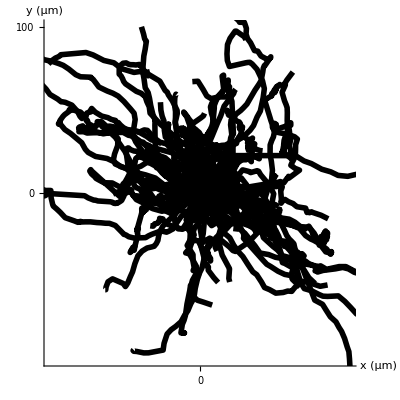

```mathematica
generic2dblob=Graphics[ {Thickness[0.01],Line[genericPositions2DAdjusted, VertexColors->genericJoinedColorArray] },Axes->True,AxesLabel->{"x (μm)   ","y (μm)  "},
Ticks-> {{0,100,200,300,400,500},{0,100,200,300,400,500}},
BaseStyle->{FontSize->14},PlotRange->{{-100,100},{-100,100}}
(*,PlotLabel->datasetname*)
]
```

## distance over time (figure)

```mathematica
genericfirstMapped = Table[Map[(Transpose[{#,Range[Length[#]]}])&,genericfirstDistances[[ind]]],{ind,numparasites}];
genericfirstDistancePerTime = Table[Map[(DeleteCases[#,x_/;MemberQ[x,"N"]])&,genericfirstMapped[[ind]]],{ind,numparasites}];

genericfirstDashedLines = Table[Flatten[Table[{Dashing[{i/400,Sqrt[i]/600}],Thickness[0.005],Line[genericfirstDistancePerTime[[ind]][[i]],VertexColors->Table[Black ,Length[genericfirstDashedLines[[ind]]]]]},{i,Length[genericfirstDistancePerTime[[ind]]]}], 1],{ind,numparasites}];
```

```mathematica
If[hassecond,

genericsecondMapped = Table[Map[(Transpose[{#,Range[Length[#]]}])&,genericsecondDistances[[ind]]],{ind,numparasites}];
genericsecondDistancePerTime = Table[Map[(DeleteCases[#,x_/;MemberQ[x,"N"]])&,genericsecondMapped[[ind]]],{ind,numparasites}];

genericsecondDashedLines = Table[Flatten[Table[{Dashing[{i/400,Sqrt[i]/600}],Thickness[0.005],Line[genericsecondDistancePerTime[[ind]][[i]],VertexColors->Table[Black ,Length[genericsecondDashedLines[[ind]]]]]},{i,Length[genericsecondDistancePerTime[[ind]]]}], 1],{ind,numparasites}];,

Remove[genericsecondMapped];
Remove[genericsecondDistancePerTime];
Remove[genericsecondDashedLines];
];
```

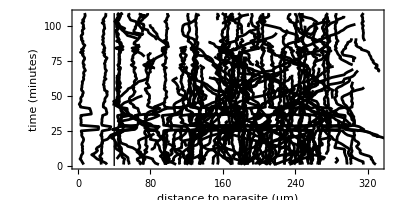

```mathematica
genericdistancesGraph = Table[Graphics[If[hassecond,{Line[Table[{40,i},{i,0,Length[genericfirstDistances[[1]][[1]]]}]],genericfirstDashedLines[[ind]],genericsecondDashedLines[[ind]]},{Line[Table[{40,i},{i,0,Length[genericfirstDistances[[1]][[1]]]}]],genericfirstDashedLines[[ind]]}],
Axes->True,
PlotRange->{{0,Max[Flatten[genericfirstDistancesWithoutN]]},{0,Length[genericfirstDistances[[1]][[1]]]}}, 
Frame->{{True,False},{True,False}},FrameLabel->{"distance to parasite (μm)","time (minutes)"},
BaseStyle->{FontSize->25},ImageSize->Full, AspectRatio->1/2,TicksStyle->18
(*,PlotLabel->datasetname <> If[numparasites>1," Parasite " <> ToString[ind],""]*)
],
{ind,numparasites}]
```

## mean speeds (figure)

```mathematica
genericspeedsHistogram =Show[histPlot[Mean[#] &/@genericfirstSpeeds,{0,10.0,0.5},{Thickness[0.006],Black}],histPlot[Mean[#] &/@genericsecondSpeeds,{0.1,10.1,0.5},{Thickness[0.006],Dashed,Blue}],
Frame->{{True,False},{True,False}},
FrameLabel->{"mean speed per cell (μm/min)","proportion of cells"},
FrameStyle->Thick,
FrameTicks-> myticks,
FrameTicksStyle->Black,
BaseStyle->{FontSize->18},
PlotRange->{0,0.9},
Epilog->{mylegend3[{ToString[Length[Mean[#] &/@genericfirstSpeeds]]<>" OT1 cells total, mean speed = " <> ToString[MyRound[Mean[Mean[#] &/@genericfirstSpeeds],2]] <> " μm/min", ToString[Length[Mean[#] &/@genericsecondSpeeds]]<> " P14 movements total, mean cells = " <> ToString[MyRound[Mean[Mean[#] &/@genericsecondSpeeds],2]] <> " μm/min"},{0.03,0.81},
FontColor->{Black,Lighter[Blue]},
SymbolShape->{"",""}
],
mylegend2noS[{"p-value = " <>ToString[MyRound[LocationTest[{Mean[#] &/@genericfirstSpeeds,Mean[#] &/@genericsecondSpeeds},Automatic,{"TestDataTable",All}][[1]][[1]][[2]][[3]],2]]},{0.09,0.67},
SymbolShape->{"", ""}]
},
Options[MyPlot]
]
```

-Graphics-

## mean turning angles (figure)

```mathematica
generictasHistogram =Show[histPlot[Flatten[genericfirstTurningAngles],{0,180.0,5.0},{Thickness[0.006],Black}],histPlot[Flatten[genericsecondTurningAngles],{0.2,180.2,5.0},{Thickness[0.006],Dashed,Blue}],
Frame->{{True,False},{True,False}},
FrameLabel->{"TA","proportion of movements"},
FrameStyle->Thick,
FrameTicks-> myticks,
FrameTicksStyle->Black,
BaseStyle->{FontSize->18},
PlotRange->{0,0.2},
Epilog->{mylegend3[{ToString[Length[Flatten[genericfirstTurningAngles]]]<>" OT1 movements total, mean TA = " <> ToString[MyRound[Mean[Flatten[genericfirstTurningAngles]],2]], ToString[Length[Flatten[genericsecondTurningAngles]]]<> " P14 movements total, mean TA = " <> ToString[MyRound[Mean[Flatten[genericsecondTurningAngles]],2]]},{0.03,0.81},
FontColor->{Black,Lighter[Blue]},
SymbolShape->{"",""}
],
mylegend2noS[{"p-value = " <> ToString[MyRound[LocationTest[{Flatten[genericfirstTurningAngles],Flatten[genericsecondTurningAngles]},Automatic,{"TestDataTable",All}][[1]][[1]][[2]][[3]],2]]},{0.07,0.67},
SymbolShape->{"", ""}]
},
Options[MyPlot]
]
```

-Graphics-

## #close over time (figure)

```mathematica
genericfirstmodelfit = Table[LinearModelFit[Table[Count[genericfirstDistances[[ind]][[All,ii]], u_ /; u <40],{ii,Length[genericfirstDistances[[ind]][[1]]]}],x,x],{ind,numparasites}];
```

```mathematica
If[hassecond,
genericsecondmodelfit = Table[LinearModelFit[Table[Count[genericsecondDistances[[ind]][[All,ii]], u_ /; u <40],{ii,Length[genericsecondDistances[[ind]][[1]]]}],x,x],{ind,numparasites}];,
Remove[genericsecondmodelfit];
];
```

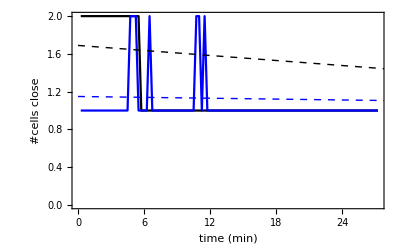

```mathematica
genericclosesGraph=Table[ListLinePlot[
If[hassecond,{Transpose[{Range[Length[genericfirstDistances[[ind]][[1]]]]/4,Table[Count[genericfirstDistances[[ind]][[All,ii]], u_ /; u <40],{ii,Length[genericfirstDistances[[ind]][[1]]]}]}],Transpose[{Range[Length[genericsecondDistances[[ind]][[1]]]]/4,Table[Count[genericsecondDistances[[ind]][[All,ii]], u_ /; u <40],{ii,Length[genericsecondDistances[[ind]][[1]]]}]}]},{Transpose[{Range[Length[genericfirstDistances[[ind]][[1]]]]/4,Table[Count[genericfirstDistances[[ind]][[All,ii]], u_ /; u <40],{ii,Length[genericfirstDistances[[ind]][[1]]]}]}]}],
Frame->{{True,False},{True,False}},
FrameLabel->{"time (min)","#cells close"}
(*,PlotLabel->datasetname <> If[numparasites>1," Parasite " <> ToString[ind],""]*),
BaseStyle->{FontSize->20},
PlotStyle->{Black,Blue},
Epilog->{If[hassecond,{{Thick,Black,Dashed,Line[{{0,genericfirstmodelfit[[ind]][0]},{Length[genericfirstDistances[[ind]][[1]]],genericfirstmodelfit[[ind]][Length[genericfirstDistances[[ind]][[1]]]]}}]},{Thick,Blue,Dashed,Line[{{0,genericsecondmodelfit[[ind]][0]},{Length[genericsecondDistances[[ind]][[1]]],genericsecondmodelfit[[ind]][Length[genericsecondDistances[[ind]][[1]]]]}}]}},{{Thick,Black,Dashed,Line[{{0,genericfirstmodelfit[[ind]][0]},{Length[genericfirstDistances[[ind]][[1]]],genericfirstmodelfit[[ind]][Length[genericfirstDistances[[ind]][[1]]]]}}]}}]
(*,mylegend3[If[hassecond,{"first slope = "<>ToString[MyRound[genericfirstmodelfit[[ind]][1]-genericfirstmodelfit[[ind]][0],2]],"second slope = "<>ToString[MyRound[genericsecondmodelfit[[ind]][1]-genericsecondmodelfit[[ind]][0],2]]},{"first slope = "<>ToString[MyRound[genericfirstmodelfit[[ind]][1]-genericfirstmodelfit[[ind]][0],2]]}],{0.03,0.81},
FontColor->{Black,Lighter[Blue]},Style->{Dashed},
SymbolShape->{"",""}
]*)
}],{ind,numparasites}]
```

## third metric (single VMF)

### cumulative

```mathematica
genericfirsttestStat = Table[Sum[Log[Evaluate[anglePDF]],{z,Table[Flatten[genericfirstAngles[[ind]]][[iiii]]*Pi/180,{iiii,Length[Flatten[genericfirstAngles[[ind]]]]}]}],{ind,numparasites}];

genericfirsttestStatResult = Table[N[Maximize[{genericfirsttestStat[[ind]]},k]],{ind,numparasites}];

genericfirsttestStat0 = Table[genericfirsttestStat[[ind]]/.k->0.000001,{ind,numparasites}];

genericfirsttestStatisticLRK = Table[-2 (genericfirsttestStat0[[ind]]-genericfirsttestStatResult[[ind]][[1]]),{ind,numparasites}];

genericfirstChiSquarePValue = Table[Probability[x ≥ genericfirsttestStatisticLRK[[ind]], x \[Distributed] ChiSquareDistribution[1]],{ind,numparasites}];

genericfirstPooledKappaPValue = Table[{ind,genericfirsttestStatResult[[ind]][[2]][[1]][[2]],genericfirstChiSquarePValue[[ind]]},{ind,numparasites}];
```

```mathematica
If[hassecond,
genericsecondtestStat = Table[Sum[Log[Evaluate[anglePDF]],{z,Table[Flatten[genericsecondAngles[[ind]]][[iiii]]*Pi/180,{iiii,Length[Flatten[genericsecondAngles[[ind]]]]}]}],{ind,numparasites}];
genericsecondtestStatResult = Table[N[Maximize[{genericfirsttestStat[[ind]]},k]],{ind,numparasites}];
genericsecondtestStat0 = Table[genericsecondtestStat[[ind]]/.k->0.000001,{ind,numparasites}];
genericsecondtestStatisticLRK = Table[-2 (genericsecondtestStat0[[ind]]-genericsecondtestStatResult[[ind]][[1]]),{ind,numparasites}];
genericsecondChiSquarePValue = Table[Probability[x ≥ genericsecondtestStatisticLRK[[ind]], x \[Distributed] ChiSquareDistribution[1]],{ind,numparasites}];
genericsecondPooledKappaPValue = Table[{ind,genericsecondtestStatResult[[ind]][[2]][[1]][[2]],genericsecondChiSquarePValue[[ind]]},{ind,numparasites}];,

Remove[genericsecondtestStat];
Remove[genericsecondtestStatResult];
Remove[genericsecondtestStat0];
Remove[genericsecondtestStatisticLRK];
Remove[genericsecondChiSquarePValue];
Remove[genericsecondPooledKappaPValue];
];
```

### cells

```mathematica
genericfirstCellstestStat = Table[Table[Sum[Log[Evaluate[anglePDF]],{z,Flatten[Select[genericfirstAngles[[ind]][[i]],#>0&]]*Pi/180}],{i,Length[genericfirstAngles[[ind]]]}],{ind,numparasites}];

genericfirstCellstestStatResult = Table[Table[N[Maximize[{genericfirstCellstestStat[[ind]][[i]]},k]],{i,Length[genericfirstCellstestStat[[ind]]]}],{ind,numparasites}];

genericfirstCellstestStat0 = Table[genericfirstCellstestStat[[ind]]/.k->0.000001,{ind,numparasites}];

genericfirstCellstestStatLRK = Table[Table[-2 (genericfirstCellstestStat0[[ind]][[i]]-genericfirstCellstestStatResult[[ind]][[i]][[1]]),{i,Length[genericfirstCellstestStat[[ind]]]}],{ind,numparasites}];

genericfirstCellstestStatChiSquarePValue = Table[Table[Probability[x ≥ genericfirstCellstestStatLRK[[ind]][[i]], x \[Distributed] ChiSquareDistribution[1]],{i,Length[genericfirstCellstestStat[[ind]]]}],{ind,numparasites}];

genericfirstCellstestKs = Table[Table[genericfirstCellstestStatResult[[ind]][[ii]][[2]][[1]][[2]],{ii,Length[genericfirstCellstestStatResult[[ind]]]}],{ind,numparasites}];

genericfirstKappaPValues = Table[Table[{ind,ii,genericfirstCellstestKs[[ind]][[ii]],genericfirstCellstestStatChiSquarePValue[[ind]][[ii]]},{ii,Length[genericfirstCellstestKs[[ind]]]}],{ind,numparasites}];
```

```mathematica
If[hassecond,

genericsecondCellstestStat = Table[Table[Sum[Log[Evaluate[anglePDF]],{z,Flatten[Select[genericsecondAngles[[ind]][[i]],#>0&]]*Pi/180}],{i,Length[genericsecondAngles[[ind]]]}],{ind,numparasites}];
genericsecondCellstestStatResult = Table[Table[N[Maximize[{genericsecondCellstestStat[[ind]][[i]]},k]],{i,Length[genericsecondCellstestStat[[ind]]]}],{ind,numparasites}];
genericsecondCellstestStat0 = Table[genericsecondCellstestStat[[ind]]/.k->0.000001,{ind,numparasites}];
genericsecondCellstestStatLRK = Table[Table[-2 (genericsecondCellstestStat0[[ind]][[i]]-genericsecondCellstestStatResult[[ind]][[i]][[1]]),{i,Length[genericsecondCellstestStat[[ind]]]}],{ind,numparasites}];
genericsecondCellstestStatChiSquarePValue = Table[Table[Probability[x ≥ genericsecondCellstestStatLRK[[ind]][[i]], x \[Distributed] ChiSquareDistribution[1]],{i,Length[genericsecondCellstestStat[[ind]]]}],{ind,numparasites}];
genericsecondCellstestKs = Table[Table[genericsecondCellstestStatResult[[ind]][[ii]][[2]][[1]][[2]],{ii,Length[genericsecondCellstestStatResult[[ind]]]}],{ind,numparasites}];
genericsecondKappaPValues = Table[Table[{ind,ii,genericsecondCellstestKs[[ind]][[ii]],genericsecondCellstestStatChiSquarePValue[[ind]][[ii]]},{ii,Length[genericsecondCellstestKs[[ind]]]}],{ind,numparasites}];,

Remove[genericsecondCellstestStat];
Remove[genericsecondCellstestStatResult];
Remove[genericsecondCellstestStat0];
Remove[genericsecondCellstestStatLRK];
Remove[genericsecondCellstestStatChiSquarePValue];
Remove[genericsecondCellstestKs];
Remove[genericsecondKappaPValues];
];
```

```mathematica
genericfirstAttractedIndices=Table[Select[genericfirstKappaPValues[[ind]],(#[[3]]>0.0 && #[[4]]<0.01)&][[All,1;;2]],{ind,numparasites}];
genericfirstRepulsedIndices=Table[Select[genericfirstKappaPValues[[ind]],(#[[3]]<0.0 && #[[4]]<0.01)&][[All,1;;2]],{ind,numparasites}];
genericfirstBiasedIndices=Table[Select[genericfirstKappaPValues[[ind]],(#[[4]]<0.01)&][[All,1;;2]],{ind,numparasites}];
genericfirstUnbiasedIndices=Table[Select[genericfirstKappaPValues[[ind]],(#[[4]]>0.01)&][[All,1;;2]],{ind,numparasites}];
```

```mathematica
If[hassecond,

genericsecondAttractedIndices=Table[Select[genericsecondKappaPValues[[ind]],(#[[3]]>0.0 && #[[4]]<0.01)&][[All,1;;2]],{ind,numparasites}];
genericsecondRepulsedIndices=Table[Select[genericsecondKappaPValues[[ind]],(#[[3]]<0.0 && #[[4]]<0.01)&][[All,1;;2]],{ind,numparasites}];
genericsecondBiasedIndices=Table[Select[genericsecondKappaPValues[[ind]],(#[[4]]<0.01)&][[All,1;;2]],{ind,numparasites}];
genericsecondUnbiasedIndices=Table[Select[genericsecondKappaPValues[[ind]],(#[[4]]>0.01)&][[All,1;;2]],{ind,numparasites}];,

Remove[genericsecondAttractedIndices];
Remove[genericsecondRepulsedIndices];
Remove[genericsecondBiasedIndices];
Remove[genericsecondUnbiasedIndices];
];
```

```mathematica
genericfirstAttractedIndices05=Table[Select[genericfirstKappaPValues[[ind]],(#[[3]]>0.0 && #[[4]]<0.05)&][[All,1;;2]],{ind,numparasites}];
genericfirstRepulsedIndices05=Table[Select[genericfirstKappaPValues[[ind]],(#[[3]]<0.0 && #[[4]]<0.05)&][[All,1;;2]],{ind,numparasites}];
genericfirstBiasedIndices05=Table[Select[genericfirstKappaPValues[[ind]],(#[[4]]<0.05)&][[All,1;;2]],{ind,numparasites}];
genericfirstUnbiasedIndices05=Table[Select[genericfirstKappaPValues[[ind]],(#[[4]]>0.05)&][[All,1;;2]],{ind,numparasites}];
```

```mathematica
If[hassecond,

genericsecondAttractedIndices05=Table[Select[genericsecondKappaPValues[[ind]],(#[[3]]>0.0 && #[[4]]<0.05)&][[All,1;;2]],{ind,numparasites}];
genericsecondRepulsedIndices05=Table[Select[genericsecondKappaPValues[[ind]],(#[[3]]<0.0 && #[[4]]<0.05)&][[All,1;;2]],{ind,numparasites}];
genericsecondBiasedIndices05=Table[Select[genericsecondKappaPValues[[ind]],(#[[4]]<0.05)&][[All,1;;2]],{ind,numparasites}];
genericsecondUnbiasedIndices05=Table[Select[genericsecondKappaPValues[[ind]],(#[[4]]>0.05)&][[All,1;;2]],{ind,numparasites}];,

Remove[genericsecondAttractedIndices05];
Remove[genericsecondRepulsedIndices05];
Remove[genericsecondBiasedIndices05];
Remove[genericsecondUnbiasedIndices05];
];
```

## third metric (mixed)

```mathematica
(* fitting vMF + sin^n distributions *)

(*eps=10;

Par0={0.08352901072749243,81.36120986743018,0.9149303275588171};
Clear[kappa1,n,f]
AllPars={kappa1,n,f};
Npar=Length[AllPars];
FitPars={1,1,1};
ParF=Table[If[FitPars[[i]]==1,AllPars[[i]],Par0[[i]]],{i,1,Npar}];
ConPars={1,1,1};

Print["Parameters to be fitted are ",Cases[AllPars*FitPars,x_?(!NumericQ[#]&)]];
Print["Parameters to be constrained (i.e. to be > 0) are ",Cases[AllPars*ConPars,x_?(!NumericQ[#]&)]];

sol3=minimum2r[Flatten[genericfirstAngles[[1]]]*Pi/180,FitVMFSin,ParF,Par0,ConPars]
If[NumericQ[sol3[[1]]],Par03=ParF/.sol3[[2]]];
genericfirstthirdmetricmultiplekappas=Par0=Par03*)
```

## third metric (turning angles)

### cells

```mathematica
genericfirstTACellstestStat = Table[Table[Sum[Log[Evaluate[anglePDF]],{z,Flatten[Select[genericfirstTurningAngles[[ind]][[i]],#>0&]]*Pi/180}],{i,Length[genericfirstTurningAngles[[ind]]]}],{ind,numparasites}];

genericfirstTACellstestStatResult = Table[Table[N[Maximize[{genericfirstTACellstestStat[[ind]][[i]]},k]],{i,Length[genericfirstTACellstestStat[[ind]]]}],{ind,numparasites}];

genericfirstTACellstestStat0 = Table[genericfirstTACellstestStat[[ind]]/.k->0.000001,{ind,numparasites}];

genericfirstTACellstestStatLRK = Table[Table[-2 (genericfirstTACellstestStat0[[ind]][[i]]-genericfirstTACellstestStatResult[[ind]][[i]][[1]]),{i,Length[genericfirstTACellstestStat[[ind]]]}],{ind,numparasites}];

genericfirstTACellstestStatChiSquarePValue = Table[Table[Probability[x ≥ genericfirstTACellstestStatLRK[[ind]][[i]], x \[Distributed] ChiSquareDistribution[1]],{i,Length[genericfirstTACellstestStat[[ind]]]}],{ind,numparasites}];

genericfirstTACellstestKs = Table[Table[genericfirstTACellstestStatResult[[ind]][[ii]][[2]][[1]][[2]],{ii,Length[genericfirstTACellstestStatResult[[ind]]]}],{ind,numparasites}];

genericfirstTAKappaPValues = Table[Table[{ind,ii,genericfirstTACellstestKs[[ind]][[ii]],genericfirstTACellstestStatChiSquarePValue[[ind]][[ii]]},{ii,Length[genericfirstTACellstestKs[[ind]]]}],{ind,numparasites}];
```

```mathematica
If[hassecond,

genericsecondTACellstestStat = Table[Table[Sum[Log[Evaluate[anglePDF]],{z,Flatten[Select[genericsecondTurningAngles[[ind]][[i]],#>0&]]*Pi/180}],{i,Length[genericsecondTurningAngles[[ind]]]}],{ind,numparasites}];
genericsecondTACellstestStatResult = Table[Table[N[Maximize[{genericsecondTACellstestStat[[ind]][[i]]},k]],{i,Length[genericsecondTACellstestStat[[ind]]]}],{ind,numparasites}];
genericsecondTACellstestStat0 = Table[genericsecondTACellstestStat[[ind]]/.k->0.000001,{ind,numparasites}];
genericsecondTACellstestStatLRK = Table[Table[-2 (genericsecondTACellstestStat0[[ind]][[i]]-genericsecondTACellstestStatResult[[ind]][[i]][[1]]),{i,Length[genericsecondTACellstestStat[[ind]]]}],{ind,numparasites}];
genericsecondTACellstestStatChiSquarePValue = Table[Table[Probability[x ≥ genericsecondTACellstestStatLRK[[ind]][[i]], x \[Distributed] ChiSquareDistribution[1]],{i,Length[genericsecondTACellstestStat[[ind]]]}],{ind,numparasites}];
genericsecondTACellstestKs = Table[Table[genericsecondTACellstestStatResult[[ind]][[ii]][[2]][[1]][[2]],{ii,Length[genericsecondTACellstestStatResult[[ind]]]}],{ind,numparasites}];
genericsecondTAKappaPValues = Table[Table[{ind,ii,genericsecondTACellstestKs[[ind]][[ii]],genericsecondTACellstestStatChiSquarePValue[[ind]][[ii]]},{ii,Length[genericsecondTACellstestKs[[ind]]]}],{ind,numparasites}];,

Remove[genericsecondTACellstestStat];
Remove[genericsecondTACellstestStatResult];
Remove[genericsecondTACellstestStat0];
Remove[genericsecondTACellstestStatLRK];
Remove[genericsecondTACellstestStatChiSquarePValue];
Remove[genericsecondTACellstestKs];
];
```

## third metric (mixed TA)

```mathematica
(* fitting 2 vMF distributions *)

(*eps=10;

Par0={0.0614005982098388,-0.0973843376699323796,0.1406294212442449};
Clear[kappa1,kappa2,f]
AllPars={kappa1,kappa2,f};
Npar=Length[AllPars];
FitPars={1,1,1};
ParF=Table[If[FitPars[[i]]==1,AllPars[[i]],Par0[[i]]],{i,1,Npar}];
ConPars={0,0,1};

Print["Parameters to be fitted are ",Cases[AllPars*FitPars,x_?(!NumericQ[#]&)]];
Print["Parameters to be constrained (i.e. to be > 0) are ",Cases[AllPars*ConPars,x_?(!NumericQ[#]&)]];

sol3=minimum2r[Flatten[genericfirstTurningAngles[[1]]]*Pi/180,FitTwoVMF,ParF,Par0,ConPars]
If[NumericQ[sol3[[1]]],Par03=ParF/.sol3[[2]]];
genericfirstturninganglemultiplekappas = Par0=Par03*)
```

## first/second metric

### angle

```mathematica
genericfirstAnglePValues = Table[N[2*Probability[(xx≥Max[genericfirstAnglesNegative[[ind]],genericfirstAnglesPositive[[ind]]]),xx\[Distributed]BinomialDistribution[(genericfirstAnglesNegative[[ind]]+genericfirstAnglesPositive[[ind]]),.5]]],{ind,numparasites}];
```

### change

```mathematica
genericfirstDistancesWithoutNMost = Table[Table[Most[genericfirstDistancesWithoutN[[ind]][[ii]]],{ii,Length[genericfirstDistancesWithoutN[[ind]]]}],{ind,numparasites}];

genericfirstListOfProbs = Table[(1/2) - (1/4) (genericfirstJumpLengths/genericfirstDistancesWithoutNMost[[ind]]),{ind,numparasites}];
genericfirstMeanProb = Table[Mean[Flatten[genericfirstListOfProbs[[ind]]]],{ind,numparasites}];
```

```mathematica
genericfirstChangePValues = Table[If[genericfirstChangeV2Negative[[ind]]≥genericfirstChangeV2Positive[[ind]],Min[N[2*Probability[xx≥Max[genericfirstChangeV2Negative[[ind]],genericfirstChangeV2Positive[[ind]]],xx\[Distributed]BinomialDistribution[(genericfirstChangeV2Negative[[ind]]+genericfirstChangeV2Negative[[ind]]),genericfirstMeanProb[[ind]]]]],1],Min[N[2*Probability[xx≤Min[genericfirstChangeV2Negative[[ind]],genericfirstChangeV2Positive[[ind]]],xx\[Distributed]BinomialDistribution[(genericfirstChangeV2Positive[[ind]]+genericfirstChangeV2Negative[[ind]]),genericfirstMeanProb[[ind]]]]],1]],{ind,numparasites}];
```

## third metric multinomial test

```mathematica
Clear[pequal];
genericfirstUnbiasedProportions = Table[Length[genericfirstUnbiasedIndices[[ind]]],{ind,numparasites}]/Table[Length[genericfirstKappaPValues[[ind]]],{ind,numparasites}];
genericfirstmultinomialdistribution = Table[MultinomialDistribution[Length[genericfirstKappaPValues[[ind]]], {(1-genericfirstUnbiasedProportions[[ind]])/2,(1-genericfirstUnbiasedProportions[[ind]])/2,genericfirstUnbiasedProportions[[ind]]}],{ind,numparasites}];

(*what's the likelihood of getting at least that many attracted cells?*)
genericfirstmultinomialtest = Table[
N[Probability[att≥Length[genericfirstAttractedIndices[[ind]]], {att, rep, unb} \[Distributed] genericfirstmultinomialdistribution[[ind]]]],{ind,numparasites}]
```

{0.483873}

```mathematica
If[hassecond,
Clear[pequal];
genericsecondUnbiasedProportions = Table[Length[genericsecondUnbiasedIndices[[ind]]],{ind,numparasites}]/Table[Length[genericsecondKappaPValues[[ind]]],{ind,numparasites}];
genericsecondmultinomialdistribution = Table[MultinomialDistribution[Length[genericsecondKappaPValues[[ind]]], {(1-genericsecondUnbiasedProportions[[ind]])/2,(1-genericsecondUnbiasedProportions[[ind]])/2,genericsecondUnbiasedProportions[[ind]]}],{ind,numparasites}];

(*what's the likelihood of getting at least that many attracted cells?*)
genericsecondmultinomialtest = Table[
N[Probability[att≥Length[genericsecondAttractedIndices[[ind]]], {att, rep, unb} \[Distributed] genericsecondmultinomialdistribution[[ind]]]],{ind,numparasites}],

Remove[genericsecondUnbiasedProportions];
Remove[genericsecondmultinomialdistribution];
Remove[genericsecondmultinomialtest];
];
```

```mathematica
(*what's the likelihood of getting more attracted than repulsed*)
(*Table[
N[Probability[att>rep, {att, rep, unb} \[Distributed] genericfirstmultinomialdistribution[[ind]]]],{ind,numparasites}]*)
```

```mathematica
Clear[pequal];
genericfirstUnbiasedProportions05 = Table[Length[genericfirstUnbiasedIndices05[[ind]]],{ind,numparasites}]/Table[Length[genericfirstKappaPValues[[ind]]],{ind,numparasites}];
genericfirstmultinomialdistribution05 = Table[MultinomialDistribution[Length[genericfirstKappaPValues[[ind]]], {(1-genericfirstUnbiasedProportions05[[ind]])/2,(1-genericfirstUnbiasedProportions05[[ind]])/2,genericfirstUnbiasedProportions05[[ind]]}],{ind,numparasites}];

genericfirstmultinomialtest05 = Table[
N[Probability[att≥Length[genericfirstAttractedIndices05[[ind]]], {att, rep, unb} \[Distributed] genericfirstmultinomialdistribution05[[ind]]]],{ind,numparasites}]
```

{0.489531}

```mathematica
If[hassecond,
Clear[pequal];
genericsecondUnbiasedProportions05 = Table[Length[genericsecondUnbiasedIndices05[[ind]]],{ind,numparasites}]/Table[Length[genericsecondKappaPValues[[ind]]],{ind,numparasites}];
genericsecondmultinomialdistribution05 = Table[MultinomialDistribution[Length[genericsecondKappaPValues[[ind]]], {(1-genericsecondUnbiasedProportions05[[ind]])/2,(1-genericsecondUnbiasedProportions05[[ind]])/2,genericsecondUnbiasedProportions05[[ind]]}],{ind,numparasites}];

genericsecondmultinomialtest05 = Table[
N[Probability[att≥Length[genericsecondAttractedIndices05[[ind]]], {att, rep, unb} \[Distributed] genericsecondmultinomialdistribution05[[ind]]]],{ind,numparasites}],

Remove[genericsecondUnbiasedProportions];
Remove[genericsecondmultinomialdistribution];
Remove[genericsecondmultinomialtest];
];
```

## analysis results (figure)

### histograms

```mathematica
genericfirstKsMin = Min[Flatten[genericfirstCellstestKs]];
genericfirstKsMax = Max[Flatten[genericfirstCellstestKs]];
genericfirstKsMean = Table[Mean[Flatten[genericfirstCellstestKs[[ind]]]],{ind,numparasites}];
genericfirstKsJump = (genericfirstKsMax-genericfirstKsMin)/40;

genericfirstPsMin = Min[Flatten[genericfirstCellstestStatChiSquarePValue]];
genericfirstPsMax = Max[Flatten[genericfirstCellstestStatChiSquarePValue]];
genericfirstPsMean = Mean[Flatten[genericfirstCellstestStatChiSquarePValue]];
genericfirstPsJump = (genericfirstKsMax-genericfirstKsMin)/40;
genericfirstBiasProportion = N[100*Map[Length[Cases[#,_?(#<0.01&)]]/Length[#]&,genericfirstCellstestStatChiSquarePValue]];
genericfirstPValuesNormalized = Table[Table[If[genericfirstCellstestStatChiSquarePValue[[ind]][[ii]]>10^-5,genericfirstCellstestStatChiSquarePValue[[ind]][[ii]],10^-5],{ii,Length[genericfirstCellstestStatChiSquarePValue[[ind]]]}],{ind,numparasites}];
```

```mathematica
If[hassecond,

genericsecondKsMin = Min[Flatten[genericsecondCellstestKs]];
genericsecondKsMax = Max[Flatten[genericsecondCellstestKs]];
genericsecondKsMean = Table[Mean[Flatten[genericsecondCellstestKs[[ind]]]],{ind,numparasites}];
genericsecondKsJump = (genericsecondKsMax-genericsecondKsMin)/40;

genericsecondPsMin = Min[Flatten[genericsecondCellstestStatChiSquarePValue]];
genericsecondPsMax = Max[Flatten[genericsecondCellstestStatChiSquarePValue]];
genericsecondPsMean = Mean[Flatten[genericsecondCellstestStatChiSquarePValue]];
genericsecondPsJump = (genericsecondKsMax-genericsecondKsMin)/40;
genericsecondBiasProportion = N[100*Map[Length[Cases[#,_?(#<0.01&)]]/Length[#]&,genericsecondCellstestStatChiSquarePValue]];
genericsecondPValuesNormalized = Table[Table[If[genericsecondCellstestStatChiSquarePValue[[ind]][[ii]]>10^-5,genericsecondCellstestStatChiSquarePValue[[ind]][[ii]],10^-5],{ii,Length[genericsecondCellstestStatChiSquarePValue[[ind]]]}],{ind,numparasites}];,

Remove[genericsecondKsMin];
Remove[genericsecondKsMax];
Remove[genericsecondKsMean];
Remove[genericsecondKsJump];
Remove[genericsecondPsMin];
Remove[genericsecondPsMax];
Remove[genericsecondPsMean];
Remove[genericsecondPsJump];
Remove[genericsecondBiasProportion];
Remove[genericsecondPValuesNormalized];
];
```

```mathematica
genericJoinedKsMin = If[hassecond,Min[genericfirstKsMin,genericsecondKsMin],genericfirstKsMin];
genericJoinedKsMax = If[hassecond,Max[genericfirstKsMax,genericsecondKsMax],genericfirstKsMax];
genericJoinedKsJump = If[hassecond,Max[genericfirstKsMax,genericsecondKsMax]-Min[genericfirstKsMin,genericsecondKsMin],genericfirstKsMax-genericfirstKsMin]/40;

genericJoinedPsMin = If[hassecond,Min[genericfirstPsMin,genericsecondPsMin],genericfirstPsMin];
genericJoinedPsMax = If[hassecond,Max[genericfirstPsMax,genericsecondPsMax],genericfirstPsMax];
genericJoinedPsJump = If[hassecond,Max[genericfirstPsMax,genericsecondPsMax]-Min[genericfirstPsMin,genericsecondPsMin],genericfirstPsMax-genericfirstPsMin]/40;
```

```mathematica
genericKsHistograms=Table[Show[If[hassecond,{histPlot[genericfirstCellstestKs[[ind]],{genericfirstKsMin,genericfirstKsMax,genericfirstKsJump},{Thickness[0.006],Black}],If[hassecond,histPlot[genericsecondCellstestKs[[ind]],{genericsecondKsMin,genericsecondKsMax,genericsecondKsJump},{Thickness[0.006],Blue}]]},histPlot[genericfirstCellstestKs[[ind]],{genericfirstKsMin,genericfirstKsMax,genericfirstKsJump},{Thickness[0.006],Black}]],
Frame->{{True,False},{True,False}},
FrameLabel->{"estimated κ_a","proportion of cells"},
FrameTicksStyle->Directive[10],
FrameStyle->Thick,
FrameTicks-> {ticksXKShort[Floor[genericJoinedKsMin],Floor[genericJoinedKsMax]],ticksYKShort[0.0,0.5]},
BaseStyle->{FontSize->18}
(*,PlotLabel->datasetname <> If[numparasites>1," Parasite " <> ToString[ind],""]*),
PlotRange->{0,0.5},
Epilog->{
mylegend3[If[hassecond,{"first OverBar[κ_a]="<>ToString[MyRound[genericfirstKsMean[[ind]],2]]<>" (n="<>ToString[Length[Flatten[genericfirstCellstestKs]]]<>")","second OverBar[κ_a]="<>ToString[MyRound[genericsecondKsMean[[ind]],2]]<>" (n="<>ToString[Length[Flatten[genericsecondCellstestKs]]]<>")"},{"first OverBar[κ_a]="<>ToString[MyRound[genericfirstKsMean[[ind]],2]]<>" (n="<>ToString[Length[Flatten[genericfirstCellstestKs]]]<>")"}],{0.28,0.92},
FontColor->{Black,Lighter[Blue]},
SymbolShape->{"", ""}
],
{Dashed,Line[{{0.0,0.0},{0.0,0.4}}]}
}
],{ind,numparasites}]
```

{-Graphics-}

```mathematica
genericCellPsHistogram = 
Table[Show[If[hassecond,{histPlot[Log10[genericfirstPValuesNormalized[[ind]]],{-4.0,0.1,0.1},{Thickness[0.006],Black}],histPlot[Log10[genericsecondPValuesNormalized[[ind]]],{-4.0,0.1,0.1},{Thickness[0.006],Blue}]},histPlot[Log10[genericfirstPValuesNormalized[[ind]]],{-4.0,0.1,0.1},{Thickness[0.006],Black}]],
Frame->{{True,False},{True,False}},
FrameLabel->{"p-value","proportion of cells"},
FrameTicksStyle->Directive[10],
FrameStyle->Thick,
FrameTicks-> {logticks3[{-5,1,1}],myticks},
BaseStyle->{FontSize->18}
(*,PlotLabel->datasetname <> If[numparasites>1," Parasite " <> ToString[ind],""]*),
PlotRange->{0,0.5},
Epilog->{
mylegend3[If[hassecond,{"first (p<0.01)="<>ToString[MyRound[genericfirstBiasProportion[[ind]],1]]<> "%","second (p<0.01)="<>ToString[MyRound[genericsecondBiasProportion[[ind]],1]]<> "%"},{"first (p<0.01)="<>ToString[MyRound[genericfirstBiasProportion[[ind]],1]]<> "%"}],{0.28,0.92},
FontColor->{Black,Lighter[Blue]},
SymbolShape->{"", ""}
],
{Dashed,Line[{{-2,0.0},{-2,0.3}}]}
}
],{ind,numparasites}]
```

{-Graphics-}

### kappa vs pvalue

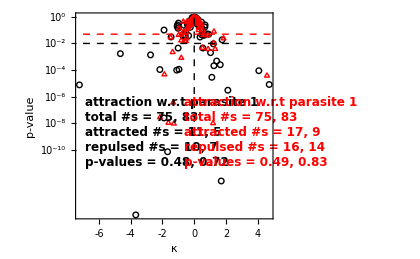

```mathematica
genericKappaPValuesFigure = Table[MyListPlot[ToLog[If[hassecond,{Transpose[{genericfirstCellstestKs[[ind]],genericfirstCellstestStatChiSquarePValue[[ind]]}],Transpose[{genericsecondCellstestKs[[ind]],genericsecondCellstestStatChiSquarePValue[[ind]]}]},{Transpose[{genericfirstCellstestKs[[ind]],genericfirstCellstestStatChiSquarePValue[[ind]]}]}]],
FrameLabel->{"κ","p-value"},
FrameTicks->{myticks,logticks3[{-10,0,1}]}
(*,PlotLabel->datasetname <> If[numparasites>1," Parasite " <> ToString[ind],""]*),
Epilog->{

{Dashed,Line[{{0,-10},{0,1}}]},
{Dashed,Line[{{-7,-2},{13,-2}}]},
{Dashed,Red,Line[{{-7,Log10[0.05]},{13,Log10[0.05]}}]},

mylegend2noS[{
"attraction w.r.t parasite "<>ToString[ind]<>
"\ntotal #s = "<>ToString[Length[genericfirstCellstestKs[[ind]]]]<>If[hassecond,", "<>ToString[Length[genericsecondCellstestKs[[ind]]]],""]<>
"\nattracted #s = "<>ToString[Count[Transpose[{genericfirstCellstestKs[[ind]],genericfirstCellstestStatChiSquarePValue[[ind]]}], u_ /; u[[1]] > 0 &&  u[[2]] <0.01]]<>If[hassecond,", "<>ToString[Count[Transpose[{genericsecondCellstestKs[[ind]],genericsecondCellstestStatChiSquarePValue[[ind]]}], u_ /; u[[1]] > 0 &&  u[[2]] <0.01]],""]<> 
"\nrepulsed #s = "<>ToString[Count[Transpose[{genericfirstCellstestKs[[ind]],genericfirstCellstestStatChiSquarePValue[[ind]]}], u_ /; u[[1]]< 0 &&  u[[2]] <0.01]]<>If[hassecond,", "<>ToString[Count[Transpose[{genericsecondCellstestKs[[ind]],genericsecondCellstestStatChiSquarePValue[[ind]]}], u_ /; u[[1]]< 0 &&  u[[2]] <0.01]],""]<>
"\np-values = "<>ToString[MyRound[genericfirstmultinomialtest[[ind]],2]]<>If[hassecond,", "<>ToString[MyRound[genericsecondmultinomialtest[[ind]],2]],""]
},{0.0,0.42}],

mylegend2noS[{
Style["attraction w.r.t parasite "<>ToString[ind]<>
"\ntotal #s = "<>ToString[Length[genericfirstCellstestKs[[ind]]]]<>If[hassecond,", "<>ToString[Length[genericsecondCellstestKs[[ind]]]],""]<>
"\nattracted #s = "<>ToString[Count[Transpose[{genericfirstCellstestKs[[ind]],genericfirstCellstestStatChiSquarePValue[[ind]]}], u_ /; u[[1]] > 0 &&  u[[2]] <0.05]]<>If[hassecond,", "<>ToString[Count[Transpose[{genericsecondCellstestKs[[ind]],genericsecondCellstestStatChiSquarePValue[[ind]]}], u_ /; u[[1]] > 0 &&  u[[2]] <0.05]],""]<> 
"\nrepulsed #s = "<>ToString[Count[Transpose[{genericfirstCellstestKs[[ind]],genericfirstCellstestStatChiSquarePValue[[ind]]}], u_ /; u[[1]]< 0 &&  u[[2]] <0.05]]<>If[hassecond,", "<>ToString[Count[Transpose[{genericsecondCellstestKs[[ind]],genericsecondCellstestStatChiSquarePValue[[ind]]}], u_ /; u[[1]]< 0 &&  u[[2]] <0.05]],""]<>
"\np-values = "<>ToString[MyRound[genericfirstmultinomialtest05[[ind]],2]]<>If[hassecond,", "<>ToString[MyRound[genericsecondmultinomialtest05[[ind]],2]],""],FontColor->Red]
},{0.50,0.42}]
}
],{ind,numparasites}]
```

## metadata (figure)

the figure labels might get messed up if there’s too little data

### biased/unbiased subarrays

```mathematica
genericfirstNumbersOfTimes = Table[Table[Length[genericfirstCorrectedWithout0[[ind]][[ii]]],{ii,Length[genericfirstCorrectedWithout0[[ind]]]}],{ind,numparasites}];
```

```mathematica
genericfirstClosestCellDistances = Table[Table[getClosestCell[ii,genericfirstCorrectedWithout0[[ind]]][[1]],{ii,Length[genericfirstCorrectedWithout0[[ind]]]}],{ind,numparasites}];
```

```mathematica
genericfirstStartingDistancesAttracted = Table[genericfirstStartingDistances[[ind]][[genericfirstAttractedIndices[[ind]][[All,2]]]],{ind,numparasites}];
genericfirstJumpLengthsAttracted = Table[genericfirstJumpLengths[[ind]][[genericfirstAttractedIndices[[ind]][[All,2]]]],{ind,numparasites}];
genericfirstSpeedsAttracted = Table[genericfirstSpeeds[[ind]][[genericfirstAttractedIndices[[ind]][[All,2]]]],{ind,numparasites}];
genericfirstNumbersOfTimesAttracted = Table[genericfirstNumbersOfTimes[[ind]][[genericfirstAttractedIndices[[ind]][[All,2]]]],{ind,numparasites}];
genericfirstClosestCellDistancesAttracted = Table[genericfirstClosestCellDistances[[ind]][[genericfirstAttractedIndices[[ind]][[All,2]]]],{ind,numparasites}];
genericfirstTAKappasAttracted = Table[genericfirstTACellstestKs[[ind]][[genericfirstAttractedIndices[[ind]][[All,2]]]],{ind,numparasites}];
```

Part::partw: Part {8,9,11,17,45,50,58,65,66,68,72} of {0.828409,0.594225,0.304137,0.682978,2.76822,1.78587,2.71156,2.07348,0.999441,1.24395,«19»,«20»,0.985453,1.97973,1.07906,1.16665,1.97836,1.29869,1.60979,3.39999,1.00595} does not exist.

Part::partw: Part {8,9,11,17,45,50,58,65,66,68,72} of {1.57572,1.13028,0.578501,1.2991,5.26545,3.39692,5.15768,3.94398,1.90104,2.36612,«19»,«17»,1.87444,3.76566,2.0525,2.2191,3.76305,2.47025,3.06198,6.46715,1.91341} does not exist.

```mathematica
genericfirstStartingDistancesRepulsed = Table[genericfirstStartingDistances[[ind]][[genericfirstRepulsedIndices[[ind]][[All,2]]]],{ind,numparasites}];
genericfirstJumpLengthsRepulsed = Table[genericfirstJumpLengths[[ind]][[genericfirstRepulsedIndices[[ind]][[All,2]]]],{ind,numparasites}];
genericfirstSpeedsRepulsed = Table[genericfirstSpeeds[[ind]][[genericfirstRepulsedIndices[[ind]][[All,2]]]],{ind,numparasites}];
genericfirstNumbersOfTimesRepulsed = Table[genericfirstNumbersOfTimes[[ind]][[genericfirstRepulsedIndices[[ind]][[All,2]]]],{ind,numparasites}];
genericfirstClosestCellDistancesRepulsed = Table[genericfirstClosestCellDistances[[ind]][[genericfirstRepulsedIndices[[ind]][[All,2]]]],{ind,numparasites}];
genericfirstTAKappasRepulsed = Table[genericfirstTACellstestKs[[ind]][[genericfirstRepulsedIndices[[ind]][[All,2]]]],{ind,numparasites}];
```

Part::partw: Part {12,24,25,37,39,43,53,56,71,73} of {0.828409,0.594225,0.304137,0.682978,2.76822,1.78587,2.71156,2.07348,0.999441,1.24395,«19»,«20»,0.985453,1.97973,1.07906,1.16665,1.97836,1.29869,1.60979,3.39999,1.00595} does not exist.

Part::partw: Part {12,24,25,37,39,43,53,56,71,73} of {1.57572,1.13028,0.578501,1.2991,5.26545,3.39692,5.15768,3.94398,1.90104,2.36612,«19»,«17»,1.87444,3.76566,2.0525,2.2191,3.76305,2.47025,3.06198,6.46715,1.91341} does not exist.

```mathematica
genericfirstStartingDistancesUnbiased = Table[genericfirstStartingDistances[[ind]][[genericfirstUnbiasedIndices[[ind]][[All,2]]]],{ind,numparasites}];
genericfirstJumpLengthsUnbiased = Table[genericfirstJumpLengths[[ind]][[genericfirstUnbiasedIndices[[ind]][[All,2]]]],{ind,numparasites}];
genericfirstSpeedsUnbiased = Table[genericfirstSpeeds[[ind]][[genericfirstUnbiasedIndices[[ind]][[All,2]]]],{ind,numparasites}];
genericfirstNumbersOfTimesUnbiased = Table[genericfirstNumbersOfTimes[[ind]][[genericfirstUnbiasedIndices[[ind]][[All,2]]]],{ind,numparasites}];
genericfirstClosestCellDistancesUnbiased = Table[genericfirstClosestCellDistances[[ind]][[genericfirstUnbiasedIndices[[ind]][[All,2]]]],{ind,numparasites}];
genericfirstTAKappasUnbiased = Table[genericfirstTACellstestKs[[ind]][[genericfirstUnbiasedIndices[[ind]][[All,2]]]],{ind,numparasites}];
```

Part::partw: Part {1,2,3,4,5,6,7,10,13,14,15,16,18,19,20,21,22,23,26,27,28,29,30,31,32,33,34,35,36,38,40,41,42,44,46,47,48,49,51,52,54,55,57,59,60,61,62,63,64,67,«4»} of {0.828409,0.594225,0.304137,0.682978,2.76822,1.78587,2.71156,2.07348,0.999441,1.24395,«19»,«20»,0.985453,1.97973,1.07906,1.16665,1.97836,1.29869,1.60979,3.39999,1.00595} does not exist.

Part::partw: Part {1,2,3,4,5,6,7,10,13,14,15,16,18,19,20,21,22,23,26,27,28,29,30,31,32,33,34,35,36,38,40,41,42,44,46,47,48,49,51,52,54,55,57,59,60,61,62,63,64,67,«4»} of {1.57572,1.13028,0.578501,1.2991,5.26545,3.39692,5.15768,3.94398,1.90104,2.36612,«19»,«17»,1.87444,3.76566,2.0525,2.2191,3.76305,2.47025,3.06198,6.46715,1.91341} does not exist.

```mathematica
genericfirstStartingDistancesBiased = Table[genericfirstStartingDistances[[ind]][[genericfirstBiasedIndices[[ind]][[All,2]]]],{ind,numparasites}];
genericfirstJumpLengthsBiased = Table[genericfirstJumpLengths[[ind]][[genericfirstBiasedIndices[[ind]][[All,2]]]],{ind,numparasites}];
genericfirstSpeedsBiased = Table[genericfirstSpeeds[[ind]][[genericfirstBiasedIndices[[ind]][[All,2]]]],{ind,numparasites}];
genericfirstNumbersOfTimesBiased = Table[genericfirstNumbersOfTimes[[ind]][[genericfirstBiasedIndices[[ind]][[All,2]]]],{ind,numparasites}];
genericfirstClosestCellDistancesBiased = Table[genericfirstClosestCellDistances[[ind]][[genericfirstBiasedIndices[[ind]][[All,2]]]],{ind,numparasites}];
genericfirstTAKappasBiased = Table[genericfirstTACellstestKs[[ind]][[genericfirstBiasedIndices[[ind]][[All,2]]]],{ind,numparasites}];
```

Part::partw: Part {8,9,11,12,17,24,25,37,39,43,45,50,53,56,58,65,66,68,71,72,73} of {0.828409,0.594225,0.304137,0.682978,2.76822,1.78587,2.71156,2.07348,0.999441,1.24395,«19»,«20»,0.985453,1.97973,1.07906,1.16665,1.97836,1.29869,1.60979,3.39999,1.00595} does not exist.

Part::partw: Part {8,9,11,12,17,24,25,37,39,43,45,50,53,56,58,65,66,68,71,72,73} of {1.57572,1.13028,0.578501,1.2991,5.26545,3.39692,5.15768,3.94398,1.90104,2.36612,«19»,«17»,1.87444,3.76566,2.0525,2.2191,3.76305,2.47025,3.06198,6.46715,1.91341} does not exist.

### figures

```mathematica
genericfirstMetadataFigureStartingDistances=Table[Show[histPlot[genericfirstStartingDistancesBiased[[ind]],{0,500,20},{Thickness[0.006],Black}],histPlot[genericfirstStartingDistancesUnbiased[[ind]],{3,503,20},{Thickness[0.006],Dashed,Blue}],
Frame->{{True,False},{True,False}},
FrameLabel->{"start distance to parasite  D (μm)","proportion of cells"},
FrameStyle->Thick,
FrameTicks-> myticks,
FrameTicksStyle->Black,
BaseStyle->{FontSize->18},
PlotRange->{0,0.4},
Epilog->{
mylegend3[{"biased (D̄="<>ToString[Mean[genericfirstStartingDistancesBiased[[ind]]]]<>" μm)", "unbiased (D̄="<>ToString[Mean[genericfirstStartingDistancesUnbiased[[ind]]]]<>" μm)"},{0.03,0.96},
FontColor->{Black,Lighter[Blue]},
SymbolShape->{"",""}
],
mylegend2noS[{"biased vs " <>ToString[Style["unbiased", Lighter[Blue]], StandardForm] <> " p="<>ToString[MyRound[LocationTest[{genericfirstStartingDistancesBiased[[ind]],genericfirstStartingDistancesUnbiased[[ind]]},0,"MannWhitney"],2]]},{0.03,0.81}]
},
Options[MyPlot]
],{ind,numparasites}]
```

{-Graphics-}

```mathematica
genericfirstMetadataFigureJumpLengths=Table[Show[histPlot[genericfirstJumpLengthsBiased[[ind]],{0,20,0.5},{Thickness[0.006],Black}],histPlot[genericfirstJumpLengthsUnbiased[[ind]],{0.3,20.3,0.5},{Thickness[0.006],Dashed,Blue}],
Frame->{{True,False},{True,False}},
FrameLabel->{"movement length/frame m (μm)","proportion of cells"},
FrameStyle->Thick,
FrameTicks-> myticks,
FrameTicksStyle->Black,
BaseStyle->{FontSize->18},
PlotRange->{0,0.4},
Epilog->{
mylegend3[{"biased (m̄="<>ToString[Mean[genericfirstJumpLengthsBiased[[ind]]]]<>" μm)", "unbiased (m̄="<>ToString[Mean[genericfirstJumpLengthsUnbiased[[ind]]]]<>" μm)"},{0.03,0.96},
FontColor->{Black,Lighter[Blue]},
SymbolShape->{"",""}
],
mylegend2noS[{"biased vs " <>ToString[Style["unbiased", Lighter[Blue]], StandardForm] <> " p="<>ToString[MyRound[LocationTest[{genericfirstJumpLengthsBiased[[ind]],genericfirstJumpLengthsUnbiased[[ind]]},0,"MannWhitney"],2]]},{0.03,0.81}]
},
Options[MyPlot]
],{ind,numparasites}]
```

HistogramList::ldata: {0.828409,0.594225,0.304137,0.682978,2.76822,1.78587,2.71156,2.07348,0.999441,«3»,0.985453,1.97973,1.07906,1.16665,1.97836,1.29869,1.60979,3.39999,1.00595}⟦{8,9,11,«15»,71,72,73}⟧ is not a valid dataset or list of datasets.

Riffle::list: List expected at position 1 in Riffle[«1»].

Riffle::list: List expected at position 1 in Riffle[Riffle[«1»],{0,0,20,20,0.5,0.5}].

General::stop: Further output of Riffle::list will be suppressed during this calculation.

Riffle::argtu: Riffle called with 1 argument; 2 or 3 arguments are expected.

General::stop: Further output of Riffle::argtu will be suppressed during this calculation.

ListLinePlot::lpn: Riffle[Riffle[Riffle[{0.828409,0.594225,0.304137,0.682978,2.76822,1.78587,2.71156,2.07348,0.999441,«4»,1.97973,1.07906,1.16665,1.97836,1.29869,1.60979,3.39999,1.00595}⟦{8,«19»,73}⟧,«1»],«1»]] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

HistogramList::ldata: {0.828409,0.594225,0.304137,0.682978,2.76822,1.78587,2.71156,2.07348,0.999441,«3»,0.985453,1.97973,1.07906,1.16665,1.97836,1.29869,1.60979,3.39999,1.00595}⟦{1,2,3,«45»,64,67,«4»}⟧ is not a valid dataset or list of datasets.

LocationTest::rctndm1: The argument {{0.828409,0.594225,0.304137,0.682978,2.76822,1.78587,2.71156,2.07348,0.999441,«18»,«19»,«20»,0.985453,1.97973,1.07906,1.16665,1.97836,1.29869,1.60979,3.39999,1.00595}⟦{«1»}⟧,«1»} at position 1 should be a rectangular array of real numbers with length greater than the dimension of the array or two such arrays of equal dimensionality.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[«1»],ListLinePlot[«1»],«7»,Epilog→{{Dashing[{0,0}],«11»},{«1»}},{BaseStyle→{FontSize→18},Axes→False,Frame→{True,True,False,False},FrameTicks→(LinTicks[#1,#2,MajorTickLength→{0.02,0},MinorTickLength→{0.,0}]&),FrameStyle→Thickness[0.005],FrameTicksStyle→Thickness[0.005],FrameLabel→{x,f},AspectRatio→1/GoldenRatio,ImageSize→{420,280}}].

{Show[ListLinePlot[Riffle[Riffle[Riffle[{0.828409,0.594225,0.304137,0.682978,2.76822,1.78587,2.71156,2.07348,0.999441,1.24395,1.27298,0.478939,0.985453,1.97973,1.07906,1.16665,1.97836,1.29869,1.60979,3.39999,1.00595}⟦{8,9,11,12,17,24,25,37,39,43,45,50,53,56,58,65,66,68,71,72,73}⟧,{8,9,11,12,17,24,25,37,39,43,45,50,53,56,58,65,66,68,71,72,73}],{0,0,20,20,0.5,0.5}]],PlotStyle→{Thickness[0.006],GrayLevel[0]},PlotRange→All],ListLinePlot[Riffle[Riffle[Riffle[{0.828409,0.594225,0.304137,0.682978,2.76822,1.78587,2.71156,2.07348,0.999441,1.24395,1.27298,0.478939,0.985453,1.97973,1.07906,1.16665,1.97836,1.29869,1.60979,3.39999,1.00595}⟦{1,2,3,4,5,6,7,10,13,14,15,16,18,19,20,21,22,23,26,27,28,29,30,31,32,33,34,35,36,38,40,41,42,44,46,47,48,49,51,52,54,55,57,59,60,61,62,63,64,67,69,70,74,75}⟧,{1,2,3,4,5,6,7,10,13,14,15,16,18,19,20,21,22,23,26,27,28,29,30,31,32,33,34,35,36,38,40,41,42,44,46,47,48,49,51,52,54,55,57,59,60,61,62,63,64,67,69,70,74,75}],{0.3,0.3,20.3,20.3,0.5,0.5}]],PlotStyle→{Thickness[0.006],Dashing[{Small,Small}],RGBColor[0, 0, 1]},PlotRange→All],Frame→{{True,False},{True,False}},FrameLabel→{movement length/frame m (μm),proportion of cells},FrameStyle→Thickness[Large],FrameTicks→(LinTicks[#1,#2,MajorTickLength→{0.02,0},MinorTickLength→{0.,0}]&),FrameTicksStyle→GrayLevel[0],BaseStyle→{FontSize→18},PlotRange→{0,0.4},Epilog→{{Dashing[{0,0}],GrayLevel[0],Thickness[0.005],Line[{Scaled[{0.03,0.97}],Scaled[{0.13,0.97}]}],Dashing[{Medium}],RGBColor[Rational[1, 3], Rational[1, 3], 1],Thickness[0.005],Line[{Scaled[{0.03,0.9}],Scaled[{0.13,0.9}]}],Text[,Scaled[{0.0675,0.965}],{-1,0}],Text[,Scaled[{0.0675,0.895}],{-1,0}],Text[biased (m̄=Mean[{0.828409, 0.594225, 0.304137, 0.682978, 2.76822, 1.78587, 2.71156, 2.07348, 0.999441, 1.24395, 1.27298, 0.478939, 0.985453, 1.97973, 1.07906, 1.16665, 1.97836, 1.29869, 1.60979, 3.39999, 1.00595}[[{8, 9, 11, 12, 17, 24, 25, 37, 39, 43, 45, 50, 53, 56, 58, 65, 66, 68, 71, 72, 73}]]] μm),Scaled[{0.135,0.96}],{-1,0}],Text[unbiased (m̄=Mean[{0.828409, 0.594225, 0.304137, 0.682978, 2.76822, 1.78587, 2.71156, 2.07348, 0.999441, 1.24395, 1.27298, 0.478939, 0.985453, 1.97973, 1.07906, 1.16665, 1.97836, 1.29869, 1.60979, 3.39999, 1.00595}[[{1, 2, 3, 4, 5, 6, 7, 10, 13, 14, 15, 16, 18, 19, 20, 21, 22, 23, 26, 27, 28, 29, 30, 31, 32, 33, 34, 35, 36, 38, 40, 41, 42, 44, 46, 47, 48, 49, 51, 52, 54, 55, 57, 59, 60, 61, 62, 63, 64, 67, 69, 70, 74, 75}]]] μm),Scaled[{0.135,0.89}],{-1,0}]},{Text[biased vs unbiased p=0.01 Round[100. LocationTest[{{0.828409, 0.594225, 0.304137, 0.682978, 2.76822, 1.78587, 2.71156, 2.07348, 0.999441, 1.24395, 1.27298, 0.478939, 0.985453, 1.97973, 1.07906, 1.16665, 1.97836, 1.29869, 1.60979, 3.39999, 1.00595}[[{8, 9, 11, 12, 17, 24, 25, 37, 39, 43, 45, 50, 53, 56, 58, 65, 66, 68, 71, 72, 73}]], {0.828409, 0.594225, 0.304137, 0.682978, 2.76822, 1.78587, 2.71156, 2.07348, 0.999441, 1.24395, 1.27298, 0.478939, 0.985453, 1.97973, 1.07906, 1.16665, 1.97836, 1.29869, 1.60979, 3.39999, 1.00595}[[{1, 2, 3, 4, 5, 6, 7, 10, 13, 14, 15, 16, 18, 19, 20, 21, 22, 23, 26, 27, 28, 29, 30, 31, 32, 33, 34, 35, 36, 38, 40, 41, 42, 44, 46, 47, 48, 49, 51, 52, 54, 55, 57, 59, 60, 61, 62, 63, 64, 67, 69, 70, 74, 75}]]}, 0., MannWhitney]],Scaled[{0.08,0.81}],{-1,0}]}},{BaseStyle→{FontSize→18},Axes→False,Frame→{True,True,False,False},FrameTicks→(LinTicks[#1,#2,MajorTickLength→{0.02,0},MinorTickLength→{0.,0}]&),FrameStyle→Thickness[0.005],FrameTicksStyle→Thickness[0.005],FrameLabel→{x,f},AspectRatio→1/GoldenRatio,ImageSize→{420,280}}]}

```mathematica
genericfirstMetadataFigureSpeeds=Table[Show[histPlot[genericfirstSpeedsBiased[[ind]],{0,20,0.5},{Thickness[0.006],Black}],histPlot[genericfirstSpeedsUnbiased[[ind]],{0.3,20.3,0.5},{Thickness[0.006],Dashed,Blue}],
Frame->{{True,False},{True,False}},
FrameLabel->{"average cell velocity v (μm/min)","proportion of cells"},
FrameStyle->Thick,
FrameTicks-> myticks,
FrameTicksStyle->Black,
BaseStyle->{FontSize->18},
PlotRange->{0,0.4},
Epilog->{
mylegend3[{"biased (v̄="<>ToString[Mean[genericfirstSpeedsBiased[[ind]]]]<>" μm/min)", "unbiased (v̄="<>ToString[Mean[genericfirstSpeedsUnbiased[[ind]]]]<>" μm/min)"},{0.03,0.96},
FontColor->{Black,Lighter[Blue]},
SymbolShape->{"",""}
],
mylegend2noS[{"biased vs " <>ToString[Style["unbiased", Lighter[Blue]], StandardForm] <> " p="<>ToString[MyRound[LocationTest[{genericfirstSpeedsBiased[[ind]],genericfirstSpeedsUnbiased[[ind]]},0,"MannWhitney"],2]]},{0.03,0.81}]
},
Options[MyPlot]
],{ind,numparasites}]
```

HistogramList::ldata: {1.57572,1.13028,0.578501,1.2991,5.26545,3.39692,5.15768,3.94398,1.90104,2.36612,«19»,«17»,1.87444,3.76566,2.0525,2.2191,3.76305,2.47025,3.06198,6.46715,1.91341}⟦{«1»}⟧ is not a valid dataset or list of datasets.

Riffle::list: List expected at position 1 in Riffle[{1.57572,1.13028,0.578501,1.2991,5.26545,3.39692,5.15768,3.94398,1.90104,«18»,«19»,«17»,1.87444,3.76566,2.0525,2.2191,3.76305,2.47025,3.06198,6.46715,1.91341}⟦{«1»}⟧,«1»].

Riffle::list: List expected at position 1 in Riffle[Riffle[{1.57572,1.13028,0.578501,1.2991,5.26545,3.39692,5.15768,3.94398,1.90104,«3»,1.87444,3.76566,2.0525,2.2191,3.76305,2.47025,3.06198,6.46715,1.91341}⟦{«1»}⟧,«1»],«1»].

General::stop: Further output of Riffle::list will be suppressed during this calculation.

Riffle::argtu: Riffle called with 1 argument; 2 or 3 arguments are expected.

General::stop: Further output of Riffle::argtu will be suppressed during this calculation.

ListLinePlot::lpn: Riffle[«1»] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

HistogramList::ldata: {1.57572,1.13028,0.578501,1.2991,5.26545,3.39692,5.15768,3.94398,1.90104,2.36612,«19»,«17»,1.87444,3.76566,2.0525,2.2191,3.76305,2.47025,3.06198,6.46715,1.91341}⟦{«1»}⟧ is not a valid dataset or list of datasets.

LocationTest::rctndm1: The argument {«1»⟦{8,9,11,12,17,24,25,37,39,43,45,50,53,56,58,65,66,68,71,72,73}⟧,{1.57572,1.13028,0.578501,1.2991,5.26545,3.39692,5.15768,3.94398,«6»,2.0525,2.2191,3.76305,2.47025,3.06198,6.46715,1.91341}⟦{1,2,«48»,«4»}⟧} at position 1 should be a rectangular array of real numbers with length greater than the dimension of the array or two such arrays of equal dimensionality.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[«1»],ListLinePlot[«1»],«7»,Epilog→{{Dashing[{0,0}],«11»},{«1»}},{BaseStyle→{FontSize→18},Axes→False,Frame→{True,True,False,False},FrameTicks→(LinTicks[#1,#2,MajorTickLength→{0.02,0},MinorTickLength→{0.,0}]&),FrameStyle→Thickness[0.005],FrameTicksStyle→Thickness[0.005],FrameLabel→{x,f},AspectRatio→1/GoldenRatio,ImageSize→{420,280}}].

{Show[ListLinePlot[Riffle[Riffle[Riffle[{1.57572,1.13028,0.578501,1.2991,5.26545,3.39692,5.15768,3.94398,1.90104,2.36612,2.42135,0.910993,1.87444,3.76566,2.0525,2.2191,3.76305,2.47025,3.06198,6.46715,1.91341}⟦{8,9,11,12,17,24,25,37,39,43,45,50,53,56,58,65,66,68,71,72,73}⟧,{8,9,11,12,17,24,25,37,39,43,45,50,53,56,58,65,66,68,71,72,73}],{0,0,20,20,0.5,0.5}]],PlotStyle→{Thickness[0.006],GrayLevel[0]},PlotRange→All],ListLinePlot[Riffle[Riffle[Riffle[{1.57572,1.13028,0.578501,1.2991,5.26545,3.39692,5.15768,3.94398,1.90104,2.36612,2.42135,0.910993,1.87444,3.76566,2.0525,2.2191,3.76305,2.47025,3.06198,6.46715,1.91341}⟦{1,2,3,4,5,6,7,10,13,14,15,16,18,19,20,21,22,23,26,27,28,29,30,31,32,33,34,35,36,38,40,41,42,44,46,47,48,49,51,52,54,55,57,59,60,61,62,63,64,67,69,70,74,75}⟧,{1,2,3,4,5,6,7,10,13,14,15,16,18,19,20,21,22,23,26,27,28,29,30,31,32,33,34,35,36,38,40,41,42,44,46,47,48,49,51,52,54,55,57,59,60,61,62,63,64,67,69,70,74,75}],{0.3,0.3,20.3,20.3,0.5,0.5}]],PlotStyle→{Thickness[0.006],Dashing[{Small,Small}],RGBColor[0, 0, 1]},PlotRange→All],Frame→{{True,False},{True,False}},FrameLabel→{average cell velocity v (μm/min),proportion of cells},FrameStyle→Thickness[Large],FrameTicks→(LinTicks[#1,#2,MajorTickLength→{0.02,0},MinorTickLength→{0.,0}]&),FrameTicksStyle→GrayLevel[0],BaseStyle→{FontSize→18},PlotRange→{0,0.4},Epilog→{{Dashing[{0,0}],GrayLevel[0],Thickness[0.005],Line[{Scaled[{0.03,0.97}],Scaled[{0.13,0.97}]}],Dashing[{Medium}],RGBColor[Rational[1, 3], Rational[1, 3], 1],Thickness[0.005],Line[{Scaled[{0.03,0.9}],Scaled[{0.13,0.9}]}],Text[,Scaled[{0.0675,0.965}],{-1,0}],Text[,Scaled[{0.0675,0.895}],{-1,0}],Text[biased (v̄=Mean[{1.57572, 1.13028, 0.578501, 1.2991, 5.26545, 3.39692, 5.15768, 3.94398, 1.90104, 2.36612, 2.42135, 0.910993, 1.87444, 3.76566, 2.0525, 2.2191, 3.76305, 2.47025, 3.06198, 6.46715, 1.91341}[[{8, 9, 11, 12, 17, 24, 25, 37, 39, 43, 45, 50, 53, 56, 58, 65, 66, 68, 71, 72, 73}]]] μm/min),Scaled[{0.135,0.96}],{-1,0}],Text[unbiased (v̄=Mean[{1.57572, 1.13028, 0.578501, 1.2991, 5.26545, 3.39692, 5.15768, 3.94398, 1.90104, 2.36612, 2.42135, 0.910993, 1.87444, 3.76566, 2.0525, 2.2191, 3.76305, 2.47025, 3.06198, 6.46715, 1.91341}[[{1, 2, 3, 4, 5, 6, 7, 10, 13, 14, 15, 16, 18, 19, 20, 21, 22, 23, 26, 27, 28, 29, 30, 31, 32, 33, 34, 35, 36, 38, 40, 41, 42, 44, 46, 47, 48, 49, 51, 52, 54, 55, 57, 59, 60, 61, 62, 63, 64, 67, 69, 70, 74, 75}]]] μm/min),Scaled[{0.135,0.89}],{-1,0}]},{Text[biased vs unbiased p=0.01 Round[100. LocationTest[{{1.57572, 1.13028, 0.578501, 1.2991, 5.26545, 3.39692, 5.15768, 3.94398, 1.90104, 2.36612, 2.42135, 0.910993, 1.87444, 3.76566, 2.0525, 2.2191, 3.76305, 2.47025, 3.06198, 6.46715, 1.91341}[[{8, 9, 11, 12, 17, 24, 25, 37, 39, 43, 45, 50, 53, 56, 58, 65, 66, 68, 71, 72, 73}]], {1.57572, 1.13028, 0.578501, 1.2991, 5.26545, 3.39692, 5.15768, 3.94398, 1.90104, 2.36612, 2.42135, 0.910993, 1.87444, 3.76566, 2.0525, 2.2191, 3.76305, 2.47025, 3.06198, 6.46715, 1.91341}[[{1, 2, 3, 4, 5, 6, 7, 10, 13, 14, 15, 16, 18, 19, 20, 21, 22, 23, 26, 27, 28, 29, 30, 31, 32, 33, 34, 35, 36, 38, 40, 41, 42, 44, 46, 47, 48, 49, 51, 52, 54, 55, 57, 59, 60, 61, 62, 63, 64, 67, 69, 70, 74, 75}]]}, 0., MannWhitney]],Scaled[{0.08,0.81}],{-1,0}]}},{BaseStyle→{FontSize→18},Axes→False,Frame→{True,True,False,False},FrameTicks→(LinTicks[#1,#2,MajorTickLength→{0.02,0},MinorTickLength→{0.,0}]&),FrameStyle→Thickness[0.005],FrameTicksStyle→Thickness[0.005],FrameLabel→{x,f},AspectRatio→1/GoldenRatio,ImageSize→{420,280}}]}

```mathematica
genericfirstMetadataFigureNumbersOfTimes=Table[Show[histPlot[genericfirstNumbersOfTimesBiased[[ind]],{0,200,5},{Thickness[0.006],Black}],histPlot[genericfirstNumbersOfTimesUnbiased[[ind]],{3,203,5},{Thickness[0.006],Dashed,Blue}],
Frame->{{True,False},{True,False}},
FrameLabel->{"number of frames per cell T","proportion of cells"},
FrameStyle->Thick,
FrameTicks-> myticks,
FrameTicksStyle->Black,
BaseStyle->{FontSize->18},
PlotRange->{0,0.4},
Epilog->{
mylegend3[{"biased (OverBar[T̄]="<>ToString[N[Mean[genericfirstNumbersOfTimesBiased[[ind]]]]]<>" frames)", "unbiased (OverBar[T̄]="<>ToString[N[Mean[genericfirstNumbersOfTimesUnbiased[[ind]]]]]<>" frames)"},{0.03,0.96},
FontColor->{Black,Lighter[Blue]},
SymbolShape->{"",""}
],
mylegend2noS[{"biased vs " <>ToString[Style["unbiased", Lighter[Blue]], StandardForm] <> " p="<>ToString[MyRound[LocationTest[{genericfirstNumbersOfTimesBiased[[ind]],genericfirstNumbersOfTimesUnbiased[[ind]]},0,"MannWhitney"],2]]},{0.03,0.81}]
},
Options[MyPlot]
],{ind,numparasites}]
```

{-Graphics-}

```mathematica
genericfirstMetadataFigureClosestCellDistances=Table[Show[histPlot[genericfirstClosestCellDistancesBiased[[ind]],{0,200,5},{Thickness[0.006],Black}],histPlot[genericfirstClosestCellDistancesUnbiased[[ind]],{3,203,5},{Thickness[0.006],Dashed,Blue}],
Frame->{{True,False},{True,False}},
FrameLabel->{"distance to the closest cell d (μm)","proportion of cells"},
FrameStyle->Thick,
FrameTicks-> myticks,
FrameTicksStyle->Black,
BaseStyle->{FontSize->18},
PlotRange->{0,0.4},
Epilog->{
mylegend3[{"biased (d̄="<>ToString[Mean[genericfirstClosestCellDistancesBiased[[ind]]]]<>" μm)", "unbiased (d̄="<>ToString[Mean[genericfirstClosestCellDistancesUnbiased[[ind]]]]<>" μm)"},{0.03,0.96},
FontColor->{Black,Lighter[Blue]},
SymbolShape->{"",""}
],
mylegend2noS[{"biased vs " <>ToString[Style["unbiased", Lighter[Blue]], StandardForm] <> " p="<>ToString[MyRound[LocationTest[{genericfirstClosestCellDistancesBiased[[ind]],genericfirstClosestCellDistancesUnbiased[[ind]]},0,"MannWhitney"],2]]},{0.03,0.81}]
},
Options[MyPlot]
],{ind,numparasites}]
```

{-Graphics-}

```mathematica
genericfirstMetadataFigureTAKappas=Table[Show[histPlot[genericfirstTAKappasBiased[[ind]],{-5,10,0.3},{Thickness[0.006],Black}],histPlot[genericfirstTAKappasUnbiased[[ind]],{-4.9,10.1,0.3},{Thickness[0.006],Dashed,Blue}],
Frame->{{True,False},{True,False}},
FrameLabel->{"persistence κ_t","proportion of cells"},
FrameStyle->Thick,
FrameTicks-> myticks,
FrameTicksStyle->Black,
BaseStyle->{FontSize->18},
PlotRange->{0,0.4},
Epilog->{
mylegend3[{"biased (OverBar[κ_t]="<>ToString[Mean[genericfirstTAKappasBiased[[ind]]]]<>")", "unbiased (OverBar[κ_t]="<>ToString[Mean[genericfirstTAKappasUnbiased[[ind]]]]<>")"},{0.03,0.96},
FontColor->{Black,Lighter[Blue]},
SymbolShape->{"",""}
],
mylegend2noS[{"biased vs " <>ToString[Style["unbiased", Lighter[Blue]], StandardForm] <> " p="<>ToString[MyRound[LocationTest[{genericfirstTAKappasBiased[[ind]],genericfirstTAKappasUnbiased[[ind]]},0,"MannWhitney"],2]]},{0.03,0.81}]
},
Options[MyPlot]
],{ind,numparasites}]
```

{-Graphics-}

## ta

```mathematica
genericTurningAnglesHistogram =Table[Show[If[hassecond,{histPlot[Flatten[genericfirstTurningAngles[[ind]]],{0,180.0,5.0},{Thickness[0.006],Black}],histPlot[Flatten[genericsecondTurningAngles[[ind]]],{0.5,180.5,5.0},{Thickness[0.006],Blue}]},histPlot[Flatten[genericfirstTurningAngles[[ind]]],{0,180.0,5.0},{Thickness[0.006],Black}]],
Frame->{{True,False},{True,False}},
FrameLabel->{"Turning angle (ϕ_t)","proportion of movements"},
FrameStyle->Thick,
FrameTicks->{Table[{i,i,{0.02,0}},{i,0,180,45}],Automatic},
FrameTicksStyle->Black,
BaseStyle->{FontSize->18},
PlotRange->{0,0.2},
Epilog->{mylegend3[If[hassecond,{ToString[Length[Flatten[genericfirstTurningAngles[[ind]]]]]<>" first movements total, mean OverBar[ϕ_t] = " <> ToString[MyRound[Mean[Flatten[genericfirstTurningAngles[[ind]]]],2]],ToString[Length[Flatten[genericfirstTurningAngles[[ind]]]]]<>" second movements total, mean OverBar[ϕ_t] = " <> ToString[MyRound[Mean[Flatten[genericsecondTurningAngles[[ind]]]],2]]},{ToString[Length[Flatten[genericfirstTurningAngles[[ind]]]]]<>" first movements total, mean OverBar[ϕ_t] = " <> ToString[MyRound[Mean[Flatten[genericfirstTurningAngles[[ind]]]],2]]}],{0.03,0.85},
FontColor->{Black,Lighter[Blue]},
SymbolShape->{"",""}
],
mylegend2noS[{"# = "<>ToString[Length[genericfirstTACellstestKs[[ind]]]]<>If[hassecond,", "<>ToString[Length[genericsecondTACellstestKs[[ind]]]],""]<>"\npersistent (κ_t>0, p<0.01) #s = "<>ToString[Count[Transpose[{genericfirstTACellstestKs[[ind]],genericfirstTACellstestStatChiSquarePValue[[ind]]}], u_ /; u[[1]] > 0 &&  u[[2]] <0.01]]<>If[hassecond,", "<>ToString[Count[Transpose[{genericsecondTACellstestKs[[ind]],genericsecondTACellstestStatChiSquarePValue[[ind]]}], u_ /; u[[1]] > 0 &&  u[[2]] <0.01]],""]<> "\naverse (κ_t<0, p<0.01) #s = "<>ToString[Count[Transpose[{genericfirstTACellstestKs[[ind]],genericfirstTACellstestStatChiSquarePValue[[ind]]}], u_ /; u[[1]]< 0 &&  u[[2]] <0.01]]<>If[hassecond,", "<>ToString[Count[Transpose[{genericsecondTACellstestKs[[ind]],genericsecondTACellstestStatChiSquarePValue[[ind]]}], u_ /; u[[1]]< 0 &&  u[[2]] <0.01]],""]<>If[hassecond,"\np-value = "<>ToString[MyRound[LocationTest[{Flatten[genericfirstTurningAngles[[ind]]],Flatten[genericsecondTurningAngles[[ind]]]},Automatic,{"TestDataTable",All}][[1]][[1]][[2]][[3]],2]],""]},{0.0,0.6}]
},
Options[MyPlot]
],{ind,numparasites}]
```

{-Graphics-}

## Every fourth

```mathematica
genericfirstCorrectedWithout0Every4th=Table[Table[genericfirstCorrectedWithout0[[ind]][[ii]][[Range[Length[genericfirstCorrectedWithout0[[ind]][[ii]]]/4]*4]],{ii,Length[genericfirstCorrectedWithout0[[ind]]]}],{ind,numparasites}];
```

```mathematica
genericfirstDistancesWithoutNEvery4th = Table[Table[genericfirstDistancesWithoutN[[ind]][[ii]][[Range[Length[genericfirstDistancesWithoutN[[ind]][[ii]]]/4]*4]],{ii,Length[genericfirstDistancesWithoutN[[ind]]]}],{ind,numparasites}];
```

```mathematica
genericfirstChangesV2WithoutNEvery4th = Table[Table[Table[(genericfirstDistancesWithoutN[[ind]][[i1]][[j1+1]] - genericfirstDistancesWithoutN[[ind]][[i1]][[j1]]),{j1,Length[genericfirstDistancesWithoutN[[ind]][[i1]]]-1}],{i1,Length[genericfirstDistancesWithoutN[[ind]]]}],{ind,numparasites}];
```

```mathematica
genericfirstJumpLengthsEvery4th = Table[Table[EuclideanDistance[genericfirstCorrectedWithout0Every4th[[i12]][[j12]],genericfirstCorrectedWithout0Every4th[[i12]][[j12+1]]],{j12,Length[genericfirstCorrectedWithout0Every4th[[i12]]] - 1}],{i12,Length[genericfirstCorrectedWithout0Every4th]}];
```

make a figure showing speeds and a figure showing turning angles

## angle with vmf

```mathematica
Par0=Par02=genericfirstthirdmetricmultiplekappas;
Show[
Histogram[genericfirstAngles[[1]],Automatic,"PDF",
ChartStyle->{GrayLevel[0.7]},
FrameTicks->{Table[{i,i,{0.02,0}},{i,0,180,45}],
LinTicks[0,0.03,MajorTickLength->{0.02,0},MinorTickLength->{0.,0}]
},
PlotRange->{{0,180},{0,0.03}},
FrameLabel->{"Angle to parasite ϕ, degrees","Frequency"},
Epilog->{
mylegend2noS[{"first (n_a="<>ToString[n0]<>")"},{-0.02,0.97},FontColor->{Black,Black}],
mylegend[{
"κ_1+κ_2",
"κ_1="<>ToString[MyRound[Par0[[1]],3]]<>" (f_1="<>ToString[MyRound[Par0[[3]],1]]<>")",
"κ_2="<>ToString[MyRound[Par0[[2]],3]]<>" (f_2="<>ToString[MyRound[1-Par0[[3]],1]]<>")"
},{0.05,0.88}]
},
Options[MyPlot]
],
MyListPlot[{
Table[{i*180/Pi,Pi/180*(Par02[[3]]*P[i,{Par02[[1]]}]+(1-Par02[[3]])*P[i,{Par02[[2]]}])},{i,0,Pi,0.01}],
Table[{i*180/Pi,Pi/180*(Par02[[3]]*P[i,{Par02[[1]]}])},{i,0,Pi,0.01}],
Table[{i*180/Pi,Pi/180*((1-Par02[[3]])*P[i,{Par02[[2]]}])},{i,0,Pi,0.01}]
},
SymbolShape->None,
PlotJoined->True
]
]
```

Part::partd: Part specification genericfirstthirdmetricmultiplekappas⟦1⟧ is longer than depth of object.

Part::partd: Part specification genericfirstthirdmetricmultiplekappas⟦3⟧ is longer than depth of object.

Part::partd: Part specification genericfirstthirdmetricmultiplekappas⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

## Exporting

```mathematica
Export[datasetname<>" 3dfigure.pdf",generic3dfigure];
Export[datasetname<>" 3dblob.pdf",generic3dblob];
Export[datasetname<>" 2dblob.pdf",generic2dblob];
Table[Export[datasetname<>" Parasite " <> ToString[ind] <>" distancesGraph.pdf",genericdistancesGraph[[ind]]],{ind,numparasites}];
Table[Export[datasetname<>" Parasite " <> ToString[ind] <>datasetname<>" closesGraph.pdf",genericclosesGraph[[ind]]],{ind,numparasites}];
Table[Export[datasetname<>" Parasite " <> ToString[ind] <>datasetname<>" KsHistograms.pdf",genericKsHistograms[[ind]]],{ind,numparasites}];
Table[Export[datasetname<>" Parasite " <> ToString[ind] <>datasetname<>" CellPsHistogram.pdf",genericCellPsHistogram[[ind]]],{ind,numparasites}];
Table[Export[datasetname<>" Parasite " <> ToString[ind] <>datasetname<>" KappaPValuesFigure.pdf",genericKappaPValuesFigure[[ind]]],{ind,numparasites}];
Table[Export[datasetname<>" Parasite " <> ToString[ind] <>datasetname<>" firstMetadataFigureStartingDistances.pdf",genericfirstMetadataFigureStartingDistances[[ind]]],{ind,numparasites}];
Table[Export[datasetname<>" Parasite " <> ToString[ind] <>datasetname<>" firstMetadataFigureJumpLengths.pdf",genericfirstMetadataFigureJumpLengths[[ind]]],{ind,numparasites}];
Table[Export[datasetname<>" Parasite " <> ToString[ind] <>datasetname<>" firstMetadataFigureSpeeds.pdf",genericfirstMetadataFigureSpeeds[[ind]]],{ind,numparasites}];
Table[Export[datasetname<>" Parasite " <> ToString[ind] <>datasetname<>" firstMetadataFigureNumbersOfTimes.pdf",genericfirstMetadataFigureNumbersOfTimes[[ind]]],{ind,numparasites}];
Table[Export[datasetname<>" Parasite " <> ToString[ind] <>datasetname<>" firstMetadataFigureClosestCellDistances.pdf",genericfirstMetadataFigureClosestCellDistances[[ind]]],{ind,numparasites}];
Table[Export[datasetname<>" Parasite " <> ToString[ind] <>datasetname<>" firstMetadataFigureTAKappas.pdf",genericfirstMetadataFigureTAKappas[[ind]]],{ind,numparasites}];
Export[datasetname<>" TurningAnglesHistogram.pdf",genericTurningAnglesHistogram];
```

```mathematica
genericexportedvalues = Join[
{{"Description","Dataset #", "Parasite #", "Cell #", "Kappa", "p-value"}},
Flatten[Table[Table[Join[{"Angle to parasite","First dataset"},genericfirstKappaPValues[[ind]][[i]]],{i,Length[genericfirstKappaPValues[[ind]]]}],{ind,numparasites}],1],
If[hassecond,Flatten[Table[Table[Join[{"Angle to parasite","Second dataset"},genericsecondKappaPValues[[ind]][[i]]],{i,Length[genericsecondKappaPValues[[ind]]]}],{ind,numparasites}],1],{}],
Flatten[Table[Table[Join[{"Turning angle","First dataset"},genericfirstTAKappaPValues[[ind]][[i]]],{i,Length[genericfirstTAKappaPValues[[ind]]]}],{ind,numparasites}],1],
If[hassecond,Flatten[Table[Table[Join[{"Turning angle","Second dataset"},genericsecondTAKappaPValues[[ind]][[i]]],{i,Length[genericsecondTAKappaPValues[[ind]]]}],{ind,numparasites}],1],{}]
];
```

```mathematica
Export[datasetname<>" exportedvalues.csv",genericexportedvalues];
```

```mathematica
(*genericfirstAnglePValues
genericfirstChangePValues
genericfirstmultinomialtest
genericsecondmultinomialtest*)
```

## (temp) collecting important stuff

```mathematica
(*SetDirectory[];
SetDirectory["Dropbox/mini_seventeen/ResearchMalaria/newdata2020"];*)
```

```mathematica
(*mynewnb = CreateNotebook[]
NotebookSave[mynewnb, "newdatasummaryFeb2021.nb"]*)
```

n5it5_shm41FrontEndObject[LinkObject["n5it5_shm", 3, 1]]41Untitled-6

```mathematica
(*nbs = Notebooks["newdatasummaryFeb2021.nb"]
nb = First[nbs]*)
```

{n5it5_shm41FrontEndObject[LinkObject["n5it5_shm", 3, 1]]41newdatasummaryFeb2021.nb/Users/viktor/Dropbox/mini_seventeen/ResearchMalaria/newdata2020/newdatasummaryFeb2021.nb}

n5it5_shm41FrontEndObject[LinkObject["n5it5_shm", 3, 1]]41newdatasummaryFeb2021.nb/Users/viktor/Dropbox/mini_seventeen/ResearchMalaria/newdata2020/newdatasummaryFeb2021.nb

```mathematica
(*SelectionMove[nb, After, Notebook];*)
```

```mathematica
(*Paste[nb,Style["20_1111 Mouse 2","Title"]]
Paste[nb,TextCell["5x10^6 Activated OT-1 cells (CMTPX labelled -RED) transferred to mice at 11:20am

5x10^6 Activated CXCR3/CCR5 KO cells (CTV labelled- Blue) transferred to mice at 11:20

1x10^5 Pb5M (GFP) Parasites injected 3:30pm 

"<>ToString[MyRound[genericfirstAverageNumberOfCellsInLive/(10^6),2]]<>"x10^6 KO cells, "<>ToString[MyRound[genericsecondAverageNumberOfCellsInLive/(10^6),2]]<>"x10^6 WT cells

Imaging commenced 7:30pm

Imaged for 3140s

Imaging frequency "<>ToString[timestep]<>"s

Imaging volume X vs Y vs Z (510 x 510 x 38um)"]]*)
```

```mathematica
(*Paste[nb, genericclosesGraph[[1]]]
Paste[nb, genericspeedsHistogram]
Paste[nb, generictasHistogram]
Paste[nb,Style["Results","Title"]]
Paste[nb,TextCell["Pooled kappa = "<>ToString[genericfirstPooledKappaPValue[[1]][[2]]]]]
Paste[nb, genericKsHistograms[[1]]]
Paste[nb, genericCellPsHistogram[[1]]]*)
```

```mathematica
(*NotebookSave[nb]*)
```